# Polarized Light Ray Tracing for Light Field Imaging with the Microscope by Rudolf Oldenbourg , Marine Biological Laboratory, Woods Hole, Massachusetts March 2022

#### Introductory Note

This Notebook is intended as a companion piece to the article entitled “The point spread function of the polarized light field microscope” by Mai Thi Tran and Rudolf Oldenbourg. In the article we present experimental results obtained with a polarized light microscope (LC-PolScope) equipped with a light field camera and compare them to numerical simulations obtained with computational methods collected in this Notebook. The numerical results are based on tracing polarized light rays through object space that is roughly 250µm × 700µm × 700µm and contains simulated birefringent sample objects. Typical sample shapes are small spheres, sheets, and rods, which populate object space and are represented by an array of voxels with uniaxial,  linear birefringence.
We determine the multitude of rays considered in this simulation by using basic concepts in geometric optics, such as the relationships between the image and object planes and the aperture plane of the microscope. Individual rays are identified by sensor pixels in the light field camera, which allows us to consider a finite set of imaging rays whose positions and directions in object space are well defined and which uniformly probe the object volume.

To see the Notes, graphics, code, etc., you need to expand the cells grouped under their headings, such as Initialization, Sample objects, Generator Code, and others.

For a first reading, expand and read the Notes for getting us started.

To view the Mathematica Notebook, read explanatory text, view images, and interact with existing graphics objects, readers can use Wolfram Player https://www.wolfram.com/player, a software package that can be freely downloaded from the Wolfram website.

To work with the code and generate your own simulations of sample objects and their light field images, you need Mathematica and some understanding of its syntax.

### Notes for getting us started

In the companion article, we lay out the reasons why we chose ray optics to simulate light field images. In doing so, we make the following assumptions and simplifications: 1) the heterogeneous sample material is transparent and only exhibits birefringence as optical anisotropy; 2) variations of the average refractive index in a sample are small; and 3) the samples are embedded in a medium that nearly matches their average refractive index. Taken together, these assumptions and simplifications justify the approximation that polarized light rays traverse object space in straight lines and maintain their overall intensity and degree of polarization while changing their polarization state due to the birefringent volume elements, or voxels, in simulated samples. This includes the assumption that the degree of polarization does not change by the interaction of light with the object. The latter justifies the use of  the Jones Calculus for simulating the changes in polarization as the light passes through a sample.

Our polarized ray tracing approach is based on the Jones Calculus to simulate the combined effect of a series of birefringent volume elements on the polarization of rays passing through the sample volume at a multitude of angles and positions. The retardance experienced by a ray passing through a single voxel is the birefringence assigned to the voxel projected onto the plane whose normal is the ray direction. The projected birefringence is then multiplied by the path length of the ray through the voxel, giving the retardance as a distance. To convert this retardance into a differential phase shift given in radian, the distance is divided by the wavelength of light and multiplied by 2π.  True to the Jones Calculus, the combined effect on a single ray that passes through a series of voxels is represented by a product series of the retardance Jones matrices of each of the voxels in the ray’s path. (In Mathematica, the multiplication scheme between Jones matrices (JM) is implemented as Dot[JM_1, JM_2, JM_3] or JM_1.JM_2.JM_3 .)  While in the experiment we actually have to send light through the sample to probe this combined effect, in the simulation we can consider the string of Dot products alone to immediately recover the retardance and slow axis orientation that is the result of stringing together the individual contributions of each volume element in the ray’s path. As such, the simulated light field directly represents the one dimensional retardance and slow axis orientation values for a multitude of rays that comprehensively probe the 3D distribution of birefringence and optic axis orientations in the sample.

Here is a brief summary of the code collected under the following headings: Initialization is defining the parameters and methods used for the simulations; Sample objects is a collection of functions that define birefringent samples, such as a birefringent ball, sheet, shell, or rod; Composites contains code that can be used to configure the object space as a composite of previously defined sample objects; Generator Code contains the code to generate light field images from individual samples or composites of samples; Simulation Results stores the results of a few simulation runs that use single objects and composites of objects; Object Space Graphics shows 3 dimensional graphics that illustrate ray traces in objects space, including their initial polarization, to build intuition in the reader and operator; the graphics can be modified after running the Graphics Initialization cell;  Playground is a group of cells that can be used to collect code ideas, inquiries, notes and graphics; Where do we go from here collects ideas how to extend this Notebook and the simulation it implements.

For consistency between the simulations and the experimental results presented in the article, we use parameters and their values that equally apply to the experiments and the simulations, including an average refractive index of n = 1.52 for object space, a magnification of 60x and numerical aperture NA = 1.2 for the microscope objective and illumination, a pixel size of 6.5µm for the camera sensor, and a pitch of 100µm and focal length of 2.5mm for the microlens array; however, these and other values can be changed by editing the Initialization cell appropriately.

More details:
To achieve an integer number of sensor pixels behind a microlens, we make the microlens pitch in our simulation equal to 16 × 6.5µm = 104µm. Hence, there are 16 × 16 sensor pixels behind a microlens. The 60x microscope objective projects the microlenses into sample space, where the pitch becomes 104µm/60 = 1.73µm. We choose to rasterize sample space by cubic voxels whose sides have voxPitch length in all three dimensions. We further choose to make voxPitch either equal to the projected microlens pitch (1.73µm) or an odd fraction of it (voxPitch = µLensPitch/3 or µLensPitch/5, etc.) Thus, projected microlenses remain centered on a voxel, which makes it easier to examine simulated light field images based on their symmetry properties. 

We are considering uni-axially birefringent samples that are rasterized in 3D by cubic voxels of voxPitch length in all three dimensions. Each voxel i has an independent optic axis orientation represented by the unit vector opticAxis_i = {opticAxisX_i, opticAxisY_i,opticAxisZ_i}, and birefringence Δn_i, which can be positive or negative. If Δn_i is zero, opticAxis_i = {0,0,0}. The retardance experienced by a ray passing through a voxel is Δn_i · Sin[α_i]^2 · l_i, where Δn_i = n_e-n_o, α_i is the angle between the optic axis and the ray direction, and l_i is the intersection length of the ray through the voxel. If Δn_i is positive, the slow axis is the unit vector along the projection of the optic axis into the plane normal to the ray direction. If Δn_i is negative, then the slow axis is orthogonal to the projected optic axis.

All distances in object space are typically given in units of the side length voxPitch of a cubic voxel. Voxels are identified by numbers that start with zero in the “lower left” corner of the sample volume that is roughly 250µm × 700µm × 700µm. The dimension parallel to the optical axis of the imaging setup is 250µm, which is also the x-axis of the laboratory coordinate system. The sample volume is spanned by only positive X, Y, and Z values.

We are choosing to rasterize object space into an odd integer number of voxels, so that the center volCtr of the object volume is in the center of a voxel. The microscope optics projects the microlens array into the sample volume at the object plane (also called nominal focus plane), which extends in the Y and Z direction and includes the center of the sample volume volCtr.

Our experimental and simulated light field images are composed of a regular array of subimages of the objective’s aperture plane. Each microlens projects a subimage that is composed of only those rays that have passed through a location (x, y, z) in object space, where (y, z) is determined by the position of the microlens in the array and x is the axial position of the focus plane in sample space. In accordance with some loss of resolution in light field imaging, the aperture image is formed by rays that have passed through location (y, z) plus-minus the microlens radius. In a recent publication [Tran, 2021], we explored the physical size of the aperture image on the camera sensor and  we were able to confirm that microscope objective lenses are designed to fulfill the Abbé sine condition. This condition states that rays that pass at a distance r from the center of the aperture disk have a tilt angle Θ in object space such that n × sinΘ / ΝΑ = r/rΝΑ, with n the refractive index of the immersion medium, NA the numerical aperture of the objective and condenser lens and rNA the radius of the edge of the projected aperture disk.  Based on these experimental findings we simulate the aperture disk behind each microlens with a radius rNA = 7.5 pixels on the camera sensor.

Some mathematical concepts and formulas are presented in the subsection Some mathematical expressions for lists and methods used in the simulation, which can be found in the Generator section. For more details see the Methods section of the companion paper.

The concept for calculating the coordinates of midpoints and intersection lengths of rays that path through object voxels was first developed by Siddon. The implementation in Mathematica used in this Notebook is by Rudolf Oldenbourg, based on Python code from Nathaniel Holderman, University of Chicago.

References
Tran, M. T. and Oldenbourg, R. (2020). An experimental method to characterize the relationship between aperture image and ray directions in microscope optics. Microsc. Res. Tech., 84(4):668-674, https://doi.org/10.1002/jemt.23625

Siddon, R. L. (1985). Fast calculation of the exact radiological path for a three-dimensional CT array. Med. Phys., 12(2):252-5. https://doi.org/10.1118/1.595715

### Initialization Evaluate first Open the grouped cells to change the voxPitch value (typically voxPitch = µLensPitch/3)

The parameter that most directly affects the accuracy of the results and the time it takes to compute them is the value of voxPitch. The smaller the voxPitch the more accurate the results (within the ray tracing approximation), but the longer it takes. The voxPitch is typically chosen to be equal to the mirolens pitch projected into object space by the microscope objective lens (e.g. voxPitch = µLensPitch = 104µm/60=1.73µm). Depending on the intricacies of the object shape, results are typically improved when choosing voxPitch = µLensPitch/3, voxPitch = µLensPitch/5, or smaller.

```mathematica
voxPitch=µLensPitch/5;voxPitch::usage="voxPitch is the side length in micron of a cubic voxel in object space;\nyou can change it to voxPitch=µLensPitch/1, or voxPitch=µLensPitch/3, voxPitch=µLensPitch/5";

λ=0.550; wavelength::usage="λ is the wavelength in µm of light propagating through the sample volume.\nIt is used to convert retardance given as Δn times the ray's path length into a phase angle and vice versa";
If[OddQ[voxNrX=Round[250/voxPitch]],,voxNrX=voxNrX+1]; voxNrX::usage="voxNrX is the number of voxels along the x-axis side of the object cube.\nAn odd number will put the Center of a voxel in the center of object space";
If[OddQ[voxNrYZ=Round[700/voxPitch]],,voxNrYZ=voxNrYZ+1]; voxNrYZ::usage="voxNrYZ is the number of voxels along the y- and z-axis side of the object cube\nAn odd number will put the Center of a voxel in the center of object space";
voxNrCtr={voxNrX/2,voxNrYZ/2,voxNrYZ/2};voxNrCtr::usage="voxNrCtr is the number location in object space on which all camera rays converge";
volCtr={voxNrX*voxPitch/2,voxNrYZ*voxPitch/2,voxNrYZ*voxPitch/2};volCtr::usage="volCtr is the center of the sample volume in µm and the location in object space on which all rays of the central microlens converge";
magnObj=60;  magnObj::usage="magnObj is the magnification of objective lens";
naObj=1.2;     naObj::usage="naObj is NA of objective lens";
nMedium=1.52;  nMedium::usage="nMedium is the refractive index of the medium in object space";
nrCamPix=16;  nrCamPix::usage="nrCamPix is the number of camera pixels behind a lenslet in the horizontal and vertical direction\n0≤i≤nrCamPix and 0≤j≤nrCamPix span the plane of camera pixels, with {i,j} Reals\nIntegers {i,j} count the pixels. {0.5,0.5} is the center location of pixel {1,1}";
camPixPitch=6.5;  camPixPitch::usage="camPixPitch is the size of the camera pixels in µm in image space";
µLensCtr={8,8}; µLensCtr::usage="µLensCtr is the microLens center position in camera pixels";
µLensPitch=nrCamPix*camPixPitch/magnObj;  µLensPitch::usage="µLens pitch in object space is about 1.733µm when using 60x objective lens.\n1.733*60=104µm is actually a bit bigger than 100µm pitch of the experimental µLens array.\n104µm makes it an integer number of camera pixels.";
rNA =7.5;  rNA::usage="rNA is the radius of the edge of the objective lens aperture in camera pixels; rNA = 7.5 for 60x/1.4NA objective lens and a condenser NA of 1.2";

(*The computation implements the Abbe sine condition for points in the back focal plane of the objective lens*)
(*Making this a delayed assignment slows down the computation tremendously*)
(*Angle values need to be converted and rounded to integer degrees, otherwise later the test for all members of mP and iL having equal length fails for all voxPitch values. I don't know why!*)
camPixRays::usage="The list camPixRays[[i,j]] holds values for azimuth and tilt angles in object space for rays originating in camera pixels {i,j} behind the central lenslet";
camPixRays=Table[If[(tmp=Sqrt[(i-0.5-µLensCtr[[1]])^2+(j-0.5-µLensCtr[[2]])^2])>rNA,{Null},
	{ArcTan[i-0.5-µLensCtr[[1]],j-0.5-µLensCtr[[2]]]/Degree,ArcSin[tmp/rNA*naObj/nMedium]/Degree}//Round],{i,nrCamPix},{j,nrCamPix}];

camRayEntrance::usage="The camRayEntrance list holds the positions where camera rays originating in pixel {i,j} pass through the entrance face into the object cube.\nThe x position of the entrance face is 0, camera rays all converge on volCtr";
camRayEntrance:=Flatten[Table[If[camPixRays[[i,j]]=={Null},,{{i,j},
		{0,volCtr[[1]]*Tan[camPixRays[[i,j,2]]Degree]Sin[camPixRays[[i,j,1]]Degree]+volCtr[[2]],
		volCtr[[1]]*Tan[camPixRays[[i,j,2]]Degree]Cos[camPixRays[[i,j,1]]Degree]+volCtr[[3]]}}],{i,nrCamPix},{j,nrCamPix}]//N,1]//DeleteCases[Null]

nrRays=Length[camRayEntrance]; nrRays::usage="nrRays is the  number of all rays (172 for naObj=1.2 and rNA=7.5; 188 for naObj=1.2 and rNA=7.7) that fall onto the camera and pass through the objective aperture";

rayEnter::usage="List of object space coordinates where rays enter object space. The x-position is 0";
rayEnter=Table[camRayEntrance[[i,2]],{i,nrRays}];

rayExit::usage="List of object space coordinates where rays exit object space. The x-position is voxPitch*voxNrX";
rayExit=Table[rayEnter[[i]]+2(volCtr-rayEnter[[i]]),{i,nrRays}];

rayUnitVectors::usage="List of 3 unit vectors,first is in the ray direction,second and third span the plane perpendicular to the ray direction
and are parallel to the y-and z-axis after rotating the ray parallel to x-axis towards camera.
All three unit vectors are orthogonal to each other.
The fourth element of the list is the rotation matrix that rotates the ray direction parallel to the x-axis
rayUnitVectors[[rayNr]]={{rayDirX,rayDirY,rayDirZ},{rayPolYX,rayPolYY,rayPolYZ},{rayPolZX,rayPolZY,rayPolZZ},{rotation matrix}}";
rayUnitVectors=Table[{tmp=Normalize[rayExit[[rayNr]]-rayEnter[[rayNr]]];tmp2=Inverse[tmp3=RotationMatrix[{tmp,{1,0,0}}]];tmp,
					tmp2.{0,1,0},tmp2.{0,0,1},tmp3},{rayNr,nrRays}];

voxRayJM::usage="voxRayJM[Δn,opticAxis,rayDir,l] generates the Jones Matrix of a 3D birefringent voxel with Δn its birefringence and opticAxis its optic axis (3D unit vector);
The output is the linear retarder Jones Matrix for the voxel, with Δn projected onto the plane normal to the ray direction;
rayDir is a list of 3 unit vectors, the first (rayDir[[1]]) points in the ray direction, the second and third vectors (rayDir[[2]], rayDir[[3]]) span the plane perpendicular to the ray direction;
rayDir[[2]] and rayDir[[3]] are parallel to the y-and z-axis, respectively, after passing through the objective lens, which rotates the ray parallel to x-axis towards the camera;
azim is the angle between rayDir[[2]] and the projection of opticAxis into the plane spanned by rayDir[[2]] and rayDir[[3]];
ret is the retardance in radian computed as Δn*(1-Cos[α])^2*l, where α is the angle between the opticAxis and rayDir[[1]] and 
l is the intersection length of the ray with the voxel";
voxRayJM[Δn_,opticAxis_,rayDir_,l_]:=Module[{azim,ret},azim=ArcTan[opticAxis.rayDir[[2]],opticAxis.rayDir[[3]]];
		If[Δn<0,azim=azim+Pi/2];
		ret=Abs[Δn](1-Power[opticAxis.rayDir[[1]],2])2Pi l/λ;  (*the retardance is proportional to the birefringence times the square of the sine of the angle betwen the optic axis and the ray direction, see e.g. Born and Wolf*)
		{{ Cos[ret/2]+I Cos[2 azim] Sin[ret/2],I Sin[2 azim] Sin[ret/2]},{I Sin[2 azim] Sin[ret/2],Cos[ret/2]-I Cos[2 azim] Sin[ret/2 ]}}];

(*general linear polarizer Jones Matrix*)
lPJM::usage="lPJM[azim], azimuth in radian";
lPJM[azim_]:=Module[{cosVal,sinVal},cosVal=N[Cos[azim]];sinVal=N[Sin[azim]];{{cosVal^2,sinVal cosVal},{sinVal cosVal,sinVal^2}}]

(*general linear retarder Jones Matrix, ret and azim in radian*)
lRJM::usage="lRJM[ret,azim], azimuth and retardance in radian";
lRJM[ret_,azim_]:={{ Cos[ret/2]-I Cos[2 azim] Sin[ret/2],-I Sin[2 azim] Sin[ret/2]},
       {-I Sin[2 azim] Sin[ret/2],Cos[ret/2]+I Cos[2 azim] Sin[ret/2 ]}};

(*retardance function calculates retardance magnitude in radian from Jones Matrix*)
jMRet::usage="jMRet[{{jM11,jM12},{jM21,jM22}}] calculates retardance in radian from Jones Matrix";
jMRet[{{jM11_,jM12_},{jM21_,jM22_}}]:=(
2ArcTan[Sqrt[-((jM12+jM21)/(jM22+jM11))^2-((jM22-jM11)/(jM22+jM11))^2]]//Re);

(*azimuth function calculates retardance azimuth in radian from Jones Matrix*)
jMAzim::usage="jMAzim[{{jM11,jM12},{jM21,jM22}}] calculates azimuth of slow axis orientation in radian from Jones Matrix;
azimuth values range between -3Pi/4 and Pi/4";
jMAzim[{{jM11_,jM12_},{jM21_,jM22_}}]:=Module[{a,b},
	a=(jM22-jM11)/(jM22+jM11)//Im;b=(jM12+jM21)/(jM11+jM22)//Im;
If[a==0&&b==0,0,ArcTan[a,b]/2+Pi/2]//Re]

jMLCPolInt::usage="jMLCPolInt[jMTable,lcA,lcB] calculates the intensity based on a Jones matrix 
in a LC-PolScope setup using lcA and lcB, in fraction of wavelength or 2Pi, for detuning the liquid crystal compensator.
jMTable can be a Jones Matrix or a 1D or 2D Array of Jones Matrices.
The output of intensities has the same dimensions as the input jMTable";
jMLCPolInt[jMTable_,lcA_,lcB_]:=Catch[Module[{dims,dimDims,int},dims=Dimensions[jMTable];dimDims=Dimensions[dims];
	If[dimDims=={1}||dimDims>4,Throw["jMTable is not a Jones Matrix or a 1D or 2D Array of Jones Matrices"]];
	If[dimDims=={2},int=Apply[Plus,Abs[lPJM[90°].lRJM[90°,135°].jMTable.lRJM[180°+lcB 2Pi,90°].lRJM[90°+lcA 2Pi,45°].{0,1}]^2]];
	If[dimDims=={3},int=Table[Apply[Plus,Abs[lPJM[90°].lRJM[90°,135°].jMTable[[i]].lRJM[180°+lcB 2Pi,90°].lRJM[90°+lcA 2Pi,45°].{0,1}]^2],{i,dims[[1]]}]];
	If[dimDims=={4},int=Table[Apply[Plus,Abs[lPJM[90°].lRJM[90°,135°].jMTable[[i,j]].lRJM[180°+lcB 2Pi,90°].lRJM[90°+lcA 2Pi,45°].{0,1}]^2],{i,dims[[1]]},{j,dims[[2]]}]];
int]];

jMLCPolAmpl::usage="jMLCPolAmpl[jMTable,lcA,lcB] calculates the light's complex amplitude based on a Jones matrix
in a LC-PolScope setup using lcA and lcB, in fraction of wavelength or 2Pi, for detuning the liquid crystal compensator.
jMTable can be a Jones Matrix or a 1D or 2D Array of Jones Matrices.
The output of amplitudes with phase has the same dimensions as the input jMTable";
jMLCPolAmpl[jMTable_,lcA_,lcB_]:=Catch[Module[{dims,dimDims,ampl},dims=Dimensions[jMTable];dimDims=Dimensions[dims];
	If[dimDims=={1}||dimDims>4,Throw["jMTable is not a Jones Matrix or a 1D or 2D Array of Jones Matrices"]];
	If[dimDims=={2},ampl=(lPJM[90°].lRJM[90°,135°].jMTable.lRJM[180°+lcB 2Pi,90°].lRJM[90°+lcA 2Pi,45°].{0,1}(*Exp[I Random[Real,{-Pi,Pi}]]*))[[2]]];  (*at the end, the amplitude can be multiplied with a random phase factor*)
	If[dimDims=={3},ampl=Table[(lPJM[90°].lRJM[90°,135°].jMTable[[i]].lRJM[180°+lcB 2Pi,90°].lRJM[90°+lcA 2Pi,45°].{0,1})[[2]],{i,dims[[1]]}]];
	If[dimDims=={4},ampl=Table[(lPJM[90°].lRJM[90°,135°].jMTable[[i,j]].lRJM[180°+lcB 2Pi,90°].lRJM[90°+lcA 2Pi,45°].{0,1})[[2]],{i,dims[[1]]},{j,dims[[2]]}]];
ampl]];

intLCPolRet::usage="intLCPolRet[data,swing] calculates the retardance in radian based on a list of LCPol intensity values using the 5-frame algorithm;
data is a list of five 2D lists of intensity values that were generated with an LC-PolScope using the following
LC detuning pairs: (0,0}; {swing,0}; {0,swing}; {0,-swing}; {-swing,0}, with swing in fraction of wavelength";
intLCPolRet[data_,swing_]:=Module[{a,b,den,prefactor,tmp},
	a=data⟦5⟧-data⟦2⟧;b=data⟦3⟧-data⟦4⟧;den=(data⟦3⟧+data⟦4⟧+data⟦2⟧+data⟦5⟧-4 data⟦1⟧)/2;prefactor=Tan[π swing];
Table[If[den⟦i,j⟧==0,Pi/2,tmp=ArcTan[prefactor Sqrt[a⟦i,j⟧^2+b⟦i,j⟧^2]/Abs[den⟦i,j⟧]];If[den⟦i,j⟧<0,Pi-tmp,tmp]],{i,Dimensions[a]⟦1⟧},{j,Dimensions[a]⟦2⟧}]]

intLCPolAzim::usage="intLCPolAzim[data,swing] calculates the azimuth in radian based on a list of LCPol intensity values using the 5-frame algorithm;
data is a list of five 2D lists of intensity values that were generated with an LC-PolScope using the following
LC detuning pairs: (0,0}; {swing,0}; {0,swing}; {0,-swing}; {-swing,0}, with swing in fraction of wavelength";
intLCPolAzim[data_,swing_]:=Module[{a,b,den},
	a=data⟦5⟧-data⟦2⟧;b=data⟦3⟧-data⟦4⟧;den=(data⟦3⟧+data⟦4⟧+data⟦2⟧+data⟦5⟧-4 data⟦1⟧)/2;
Table[If[a⟦i,j⟧==0&&b⟦i,j⟧==0,0,Pi/2+ArcTan[b⟦i,j⟧,a⟦i,j⟧]/2],{i,Dimensions[a]⟦1⟧},{j,Dimensions[a]⟦2⟧}]]

showRetAndAzimLines::usage="showRetAndAzimLines[{retList,azimList},{min_,max_},scale_,length_,thickness_,hue_,threshold_,imageSize_]
The azimList is given in radian; variable length of azim line: length = 1 makes line equal to fixed length;
variable line thickness, typically 0.005, change the multiplier in PointSize[2 thickness] in definition in the line beginning with Graphics[...
imageSize at the end of the parameter list is given in number of pixels; the function adds a 4.3% margin, which corresponds to the margin of the Graphics[] drawing";
showRetAndAzimLines[{retList_,azimList_},{min_,max_},scale_,length_,thickness_,hue_,threshold_,imageSize_]:=
	Module[{lineList,pointList,dim1,dim2},If[Dimensions[retList]≠Dimensions[azimList],Print["Error! magnList and azimList must have same dimensions"],
	dim1 =Dimensions[azimList][[1]]-scale+1;dim2 =Dimensions[azimList][[2]]-scale+1;lineList={};
	For[i=scale,i≤dim2,i+=scale,For[j=scale,j≤dim1,j+=scale,If[retList[[j,i]]>=threshold,AppendTo[lineList,{{i-0.5-scale*length*0.5Cos[azimList[[j,i]]],j-0.5+scale*length*0.5Sin[azimList[[j,i]]]},{i-0.5+scale*length*0.5Cos[azimList[[j,i]]],j-0.5-scale*length*0.5Sin[azimList[[j,i]]]}}]]]];
	pointList={};
For[i=scale,i≤dim2,i+=scale,For[j=scale,j≤dim1,j+=scale,If[retList[[j,i]]>threshold,AppendTo[pointList,{i-0.5,j-0.5}]]]];
pointList=Partition[Flatten[pointList],2];
Graphics[{Raster[retList,{{0,0},Reverse[Dimensions[retList]]}, {min,max}],Hue[hue[[1]],hue[[2]],hue[[3]] ],Thickness[thickness],Map[Line,lineList,1],PointSize[0.5thickness],Map[Point,pointList,1]},ImageSize->imageSize]]] 

voxPitchList::usage="voxPitchList={voxPitch,voxPitch,voxPitch}";
voxPitchList={voxPitch,voxPitch,voxPitch};

voxNrList::usage="voxNrList={voxNrX,voxNrYZ,voxNrYZ}";
voxNrList={voxNrX,voxNrYZ,voxNrYZ};

(*Siddon algorithms, Mathematica implementation by Rudolf Oldenbourg, March 2019, based on Python code from Nathaniel Holderman, UChicago, in 2018*)
(*pixNumXIn is the number of voxels in x-direction between entrance face and front face of bounding object box. The same applies to y- and z-direction*)
(*pixNumXOut is the number of voxels in x-direction between entrance face and back face of bounding object box. The same applies to y- and z-direction*)
(*dx_,dy_, and dz_ must be Real numbers, not integers*)
rayTrace[{x1_,y1_,z1_},{x2_,y2_,z2_},{dx_,dy_,dz_},{{pixNumXIn_,pixNumXOut_},{pixNumYIn_,pixNumYOut_},{pixNumZIn_,pixNumZOut_}}]:=
(*Catch[*)Module[{ax={},ax0,axN,ay={},ay0,ayN,az={},az0,azN,aMin,aMax,iMin,iMax,jMin,jMax,kMin,kMax},
(*first,compute starting and ending parametric values in each dimension*)
		If[x2-x1≠0,ax0=(pixNumXIn dx-x1)/(x2-x1);axN=(pixNumXOut*dx-x1)/(x2-x1),ax0=0.;axN=1.];
		If[y2-y1≠0,ay0=(pixNumYIn dy-y1)/(y2-y1);ayN=(pixNumYOut*dy-y1)/(y2-y1),ay0=0.;ayN=1.];
		If[z2-z1≠0,az0=(pixNumZIn dz-z1)/(z2-z1);azN=(pixNumZOut*dz-z1)/(z2-z1),az0=0.;azN=1.];
(*Print["ax0=",ax0,", axN=",axN,", ay0=",ay0,", ayN=",ayN,", az0=",az0,", azN=",azN];*)
(*then calculate absolute max and min parametric values*)
		aMin=Max[0.,Min[ax0,axN],Min[ay0,ayN],Min[az0,azN]];
		aMax=Min[1.,Max[ax0,axN],Max[ay0,ayN],Max[az0,azN]];
(*Print["aMin=",aMin,", aMax=",aMax];*)
(*now find range of indices corresponding to max/min a values*)
(*in this application, (x2-x1) is always greater zero*)
(*		iMin=Ceiling[(aMin*(x2-x1)-x1)/dx];iMax=Floor[1+(x1+aMax*(x2-x1))/dx];*)
		iMin=Ceiling[pixNumXOut-(pixNumXOut*dx-aMin*(x2-x1)-x1)/dx];iMax=Floor[1+(x1+aMax*(x2-x1))/dx];
		If[(y2-y1)≥0,
			jMin=Ceiling[pixNumYOut-(pixNumYOut*dy-aMin*(y2-y1)-y1)/dy];jMax=Floor[1+(y1+aMax*(y2-y1))/dy],
			jMin=Ceiling[pixNumYOut-(pixNumYOut*dy-aMax*(y2-y1)-y1)/dy];jMax=Floor[1+(y1+aMin*(y2-y1))/dy]];
		If[(z2-z1)≥0,
			kMin=Ceiling[pixNumZOut-(pixNumZOut*dz-aMin*(z2-z1)-z1)/dz];kMax=Floor[1+(z1+aMax*(z2-z1))/dz],
			kMin=Ceiling[pixNumZOut-(pixNumZOut*dz-aMax*(z2-z1)-z1)/dz];kMax=Floor[1+(z1+aMin*(z2-z1))/dz]];
(*Print["iMin=",iMin,", iMax=",iMax,", jMin=",jMin,", jMax=",jMax,", kMin=",kMin,", kMax=",kMax];*)
(*next calculate the list of parametric values for each coordinate*)
		For [i=iMin,i<iMax,i++,ax=Append[ax,(i*dx-x1)/(x2-x1)]];
		If [y2-y1>0,For [j=jMin,j<jMax,j++,ay=Append[ay,(j*dy-y1)/(y2-y1)]]];
		If [y2-y1<0,For [j=jMin,j<jMax,j++,ay=Prepend[ay,(j*dy-y1)/(y2-y1)]]];
		If [z2-z1>0,For [k=kMin,k<kMax,k++,az=Append[az,(k*dz-z1)/(z2-z1)]]];
		If [z2-z1<0,For [k=kMin,k<kMax,k++,az=Prepend[az,(k*dz-z1)/(z2-z1)]]];
(*Print["ax=",ax];
Print["ay=",ay];
Print["az=",az];
Throw["thrown"];*)
(*finally,form the list of parametric values*)
		Union[{aMin},ax,ay,az,{aMax}]]
(*	]*)

midPoints[{x1_,y1_,z1_},{x2_,y2_,z2_},{dx_,dy_,dz_},{{pixNumXIn_,pixNumXOut_},{pixNumYIn_,pixNumYOut_},{pixNumZIn_,pixNumZOut_}}]:=
	Module[{aList,x,y,z,iMid},
		aList=rayTrace[{x1,y1,z1},{x2,y2,z2},{dx,dy,dz},{{pixNumXIn,pixNumXOut},{pixNumYIn,pixNumYOut},{pixNumZIn,pixNumZOut}}];
(*loop through, computing midpoints for each adjacent pair of a values for chosen coord*)
		iMid={};
		For[m =2,m≤Length[aList],m++,
			x=.5*(aList[[m]]+aList[[m-1]])*(x2-x1)+x1;
			y=.5*(aList[[m]]+aList[[m-1]])*(y2-y1)+y1;
			z=.5*(aList[[m]]+aList[[m-1]])*(z2-z1)+z1;
			iMid=Append[iMid,{x,y,z}]];
	iMid]

intersectLength[{x1_,y1_,z1_},{x2_,y2_,z2_},{dx_,dy_,dz_},{{pixNumXIn_,pixNumXOut_},{pixNumYIn_,pixNumYOut_},{pixNumZIn_,pixNumZOut_}}]:=
	Module[{aList,lengths},
		aList=rayTrace[{x1,y1,z1},{x2,y2,z2},{dx,dy,dz},{{pixNumXIn,pixNumXOut},{pixNumYIn,pixNumYOut},{pixNumZIn,pixNumZOut}}];
(*find length of intersection by multiplying difference in parametric values by total ray length*)
		lengths={};
		For[m =2,m≤Length[aList],m++,
			lengths=Append[lengths,Sqrt[(x2-x1)^2+(y2-y1)^2+(z2-z1)^2]*(aList[[m]]-aList[[m-1]])]];
	lengths]
```

### Sample objects Evaluate at least one sample object for simulating a light field image. You can also evaluate all grouped cells together to define all samples at once All lengths given in units of voxPitch, all angles in radian

All sample functions and their composites generate a list that has three elements on the first level: The first element is a list of metadata such as the object size in voxPitch units, and the voxPitch in µm that was used to generate the sample list. To show the metadata, print the first list element. The second element is a 3D list of the birefringence (a scalar) of each voxel of the sample. The third element is a 3D list of a 3D vector for each voxel, where each vector indicates the orientation of the optic axis of a birefringent voxel. When the birefringence is zero, the vector is {0,0,0}. The second and third elements are 3D lists with the same number of elements, namely the number of voxels that represent the sample object.
In the list of metadata, the second element must be the list of X, Y, and Z numbers of voxels in the x-, y-, and z-directions. {X, Y, Z} represents the size of the box that contains the object.

#### Birefringent ball, ballBir[radius,Δn,theta,azim], is a solid ball made of birefringent (Δn≠0) material. The ball’s diameter is made to be an odd number of voxPitch, including one, with its center in the center of a voxel (radius=0 will result in a ball radius of 0.5 voxPitch). The material has an optic axis, whose orientation is defined by angles azim and theta and is represented by a vector of length 1. For azim=theta=0, the optic axis is oriented parallel to the x-axis. The axis can be rotated around the y-axis by the angle theta [in radian] away from the x-axis, and then rotated by azim [in radian] around the x-axis. The birefringence Δn can be positive or negative, and if Δn=0, the optic axis is {0,0,0}. Δn and the optic axis are the same for every voxel of the ball. The birefringence of voxels near the edge of the object can be fractions of Δn.

```mathematica
ballBir::usage="ballBir[radius,Δn,theta,azim], is a solid ball made of birefringent (Δn≠0) material. Angles in radian and radius in units of voxPitch.
The ball's diameter is made to be an odd number of voxPitch, including one, with its center in the center of a voxel (radius=0 will result in a ball radius of 0.5 voxPitch). 
The material has an optic axis, whose orientation is defined by angles azim and theta (in radian) and is represented by a vector of length 1. 
For azim=theta=0, the optic axis is oriented parallel to the x-axis. The axis can be rotated around the y-axis by the angle theta away from the x-axis, and then rotated by azim [in radian] around the x-axis. 
The birefringence Δn can be positive or negative, and if Δn=0, the optic axis is {0,0,0}. Δn and the optic axis are the same for every voxel of the ball. The birefringence of voxels near the edge of the object can be fractions of Δn.";

ballBir[radius_,Δn_,theta_,azim_]:=
Module[{r,rotAzim,rotTheta,smpRegion,smpBounds,rSize,ΔnArray,opticAxis,opticAxisArray},
If[radius==0,r=0.5,r=radius];
rotTheta=RotationMatrix[theta,{0,1,0}];
rotAzim=RotationMatrix[azim ,{1,0,0}];
opticAxis=rotAzim.(rotTheta.{1,0,0});
smpRegion=Region@Ball[{0,0,0},r];
smpBounds=RegionBounds[smpRegion];
rSize=Ceiling[(Transpose[smpBounds][[2]]-Transpose[smpBounds][[1]])];Do[If[EvenQ[rSize[[i]]],rSize[[i]]+=1],{i,3}];(*raster size, it changes the radius to an integer number of voxels plus 0.5*)
ΔnArray=Reverse[ImageData[RegionImage[smpRegion,RegionBounds[smpRegion],RasterSize->rSize]]Δn,{1,2}];
opticAxisArray=Table[If[ΔnArray[[k,j,i]]≠0,opticAxis,{0,0,0}],{k,rSize[[3]]},{j,rSize[[2]]},{i,rSize[[1]]}]; (*array of normalized vectors*)
{{"Ball box {X,Y,Z}=",rSize,", radius=",rSize[[1]]/2//N,", all in units of voxPitch=",voxPitch,"µm, birefringence=",Δn,", rotation theta=",theta,", rotation azim=",azim},ΔnArray,opticAxisArray}]
```

Graphics

```mathematica
?ballBir
```

```mathematica
smp=ballBir[1.5,-0.172,10°,0°];
Print@@smp[[1]];
Graphics3D[Raster3D[smp[[2]]/smp[[1,8]],ColorFunction->"GrayLevelOpacity"]]
tmp2=DeleteCases[Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2],Null];
Graphics3D[{Red,Map[Line,tmp2]},ImageSize->200]
```

Ball box {X,Y,Z}={3,3,3}, radius=1.5, all in units of voxPitch=0.346667µm, birefringence=-0.172, rotation theta=10 °, rotation azim=0

-Graphics3D-

-Graphics3D-

#### Birefringent sheet, sheetBir[radius,thickness,Δn,theta,azim], angles in radian, radius and thickness in units of voxPitch of a birefringent (Δn) sheet (cylinder) that extends in the y-z plane. Its optic axis opticAxis has an inclination angle theta to x-axis and an azimuth angle (azim) in the y-z plane measured from the z-axis. The birefringence Δn can be positive or negative, and if Δn=0, the optic axis is {0,0,0}. Δn and the optic axis are the same for every voxel of the sheet. The birefringence of voxels near the edge of the object can be fractions of Δn. Stack of birefringent sheets, stackBir[{sheetBir[],sheetBir[],...}]

```mathematica
sheetBir::usage="sheetBir[radius,thickness,Δn,theta,azim], angles in radian, radius and thickness in units of voxPitch of a birefringent (Δn) sheet (cylinder) that extends in the y-z plane. 
A radius ending in .5 puts the center of the sheet in the center of a voxel in the Y-Z plane
An odd integer thickness puts the center of the sheet in the center of a voxel in the X-direction";

sheetBirStack::usage="sheetBirStack[sheetList] combines a stack of birefringent sheets into a single object. The input is a list of sheetBir[]functions 
each of which has as input the thickness, Δn, and optic axis orientation of the individual sheet. All sheets must have the same radius.
sheetBirStack[] combines the ΔnArrays and opticAxisArrays of the individual sheets and converts them to a single object";

sheetBir[radius_,thick_,Δn_,theta_,azim_]:=
Module[{opticAxis,rotAzim,rotTheta,smpRegion,smpBounds,rSize,ΔnArray,opticAxisArray},
rotTheta=RotationMatrix[theta,{0,1,0}];
rotAzim=RotationMatrix[azim,{1,0,0}];
opticAxis=Normalize[rotAzim.(rotTheta.{1,0,0})];
smpRegion=Region@Cylinder[{{-thick/2,0,0},{thick/2,0,0}},radius];
smpBounds=RegionBounds[smpRegion];
rSize=Round[(Transpose[smpBounds][[2]]-Transpose[smpBounds][[1]])];
ΔnArray=Reverse[ImageData[RegionImage[smpRegion,RegionBounds[smpRegion],RasterSize->rSize]]Δn,{1,2}];
opticAxisArray=Table[If[ΔnArray[[k,j,i]]≠0,opticAxis,{0,0,0}],{k,rSize[[3]]},{j,rSize[[2]]},{i,rSize[[1]]}];
{{"Sheet box {X,Y,Z}=",rSize,", radius=",radius,", sheet thickness=",thick,", all in units of voxPitch=",voxPitch,"µm, birefringence=",Δn,", rotation theta=",theta,", rotation azim=",azim} ,ΔnArray,opticAxisArray}]

sheetBirStack[sheetList_]:=
Catch[Module[{num,thickList,r,ΔnList,stackThick,smpRegion,smpBounds,rSize,ΔnArray,opticAxisArray},
num=Length[sheetList];(*number of sheets in the stack*)
r=sheetList[[1,1,4]]; If[Table[r,num]≠Table[sheetList[[i,1,4]],{i,num}],Throw["All sheets must have the same radius"]];
ΔnList=Table[sheetList[[i,1,10]],{i,num}];
thickList=Table[sheetList[[i,1,6]],{i,num}];
stackThick=Plus@@thickList;
ΔnArray=Transpose[sheetList[[1,2]],{3,2,1}];
opticAxisArray=Transpose[sheetList[[1,3]],{3,2,1}];
For[i=2,i≤num,i++,
	ΔnArray=Join[ΔnArray,Transpose[sheetList[[i,2]],{3,2,1}]];
	opticAxisArray=Join[opticAxisArray,Transpose[sheetList[[i,3]],{3,2,1}]]
	];
ΔnArray=Transpose[ΔnArray,{3,2,1}];
opticAxisArray=Transpose[opticAxisArray,{3,2,1}];
rSize=Reverse[Dimensions[ΔnArray]];
{{"Sheet stack box {X,Y,Z}=",rSize,", radius=",r,", number of sheets = ",num,", Δn List =",ΔnList,", stack thickness = ",stackThick,", all length in units of voxPitch = ",voxPitch,"µm"},ΔnArray,opticAxisArray}]]
```

Graphics

```mathematica
?sheetBir
```

```mathematica
?sheetBirStack
```

```mathematica
sheetRadius=7.5;
sheetBirList1={sheetBir[3.5,3,0.1,0°,0°]};
sheetBirList2={sheetBir[sheetRadius,2,0.2,0°,0°],sheetBir[sheetRadius,4,0.1,90°,0°]};
sheetBirList3={sheetBir[7.5,3,0.1,0°,0°],sheetBir[7.5,1,0.2,90°,0°],sheetBir[7.5,2,0.05,45°,45°]};
```

```mathematica
(*smp=sheetBir[sheetRadius,3,0.1,10°,0];*)
smp=sheetBirStack[sheetBirList3];
Catch[If[%=="All sheets must have the same radius",Throw["All sheets must have the same radius"]];
Print@@smp[[1]];
If[smp[[1,1]]=="Sheet box {X,Y,Z}=",Graphics3D[Raster3D[smp[[2]]/smp[[1,10]],ColorFunction->"GrayLevelOpacity"]]//Print];
If[smp[[1,1]]=="Sheet stack box {X,Y,Z}=",ΔnMax=Max[smp[[1,8]]];Graphics3D[Raster3D[smp[[2]]/ΔnMax,ColorFunction->"GrayLevelOpacity"]]//Print];
tmp1=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Graphics3D[{Red,Map[Line,tmp1]},ImageSize->200]]
```

Sheet stack box {X,Y,Z}={6,15,15}, radius=7.5, number of sheets = 3, Δn List ={0.1,0.2,0.05}, stack thickness = 6, all length in units of voxPitch = 0.346667µm

-Graphics3D-

-Graphics3D-

#### Birefringent cuboid, cuboidBir[sideX,sideY,sideZ,Δn,theta,azim], with sides of length sideX, sideY, sideZ in units of voxPitch, and birefringence Δn. Its optic axis opticAxis has a tilt angle theta to the x-axis and an azimuth angle (azim) in the y-z plane measured from the z-axis. The birefringence Δn can be positive or negative, and if Δn=0, the optic axis is {0,0,0}. Δn and the optic axis are the same for every voxel of the cuboid. Series of birefringent cuboids stacked along the Y direction stackYCuboidBir[cuboidList]

```mathematica
cuboidBir::usage="cuboidBir[sideX,sideY,sideZ,Δn,theta,azim], angles in radian, length in units of voxPitch, and birefringence Δn. 
A birefringent cuboid whose optic axis opticAxis has a tilt angle theta to the x-axis and an azimuth angle (azim) in the y-z plane measured from the z-axis. 
The birefringence Δn can be positive or negative, and if Δn=0, the optic axis is {0,0,0}. Δn and the optic axis are the same for every voxel of the cuboid.";

cuboidStackYBir::usage="cuboidStackYBir[cuboidList] combines a list of cuboids into a single object that represents a stack along Y of birefringent cuboids separated along Y; 
all cuboids must have the same dimensions in X and Z, but can differ in Y and in their Δn values and slow axis orientations";

cuboidBir[sideX_,sideY_,sideZ_,Δn_,theta_,azim_]:=
Module[{opticAxis,rotAzim,rotTheta,smpRegion,smpBounds,cuboidBox,ΔnArray,opticAxisArray},
rotTheta=RotationMatrix[theta,{0,1,0}];
rotAzim=RotationMatrix[azim,{1,0,0}];
opticAxis=Normalize[rotAzim.(rotTheta.{1,0,0})];
cuboidBox={sideX,sideY,sideZ}//Round;
ΔnArray=Table[Δn,{k,cuboidBox[[3]]},{j,cuboidBox[[2]]},{i,cuboidBox[[1]]}];
opticAxisArray=Table[If[ΔnArray[[k,j,i]]≠0,opticAxis,{0,0,0}],{k,cuboidBox[[3]]},{j,cuboidBox[[2]]},{i,cuboidBox[[1]]}];
{{"cuboid box {X,Y,Z}=",cuboidBox,", in units of voxPitch=",voxPitch,"µm, birefringence=",Δn,", rotation theta=",theta,", rotation azim=",azim},ΔnArray,opticAxisArray}]

cuboidStackYBir[cuboidList_]:=
Catch[Module[{num,sideYList,sideYStack,ΔnList,stackThick,smpRegion,smpBounds,stackBox,ΔnArray,opticAxisArray},
num=Length[cuboidList];(*number of cuboids in the stack*)
 If[Table[{cuboidList[[1,1,2,1]],cuboidList[[1,1,2,3]]},num]≠Table[{cuboidList[[i,1,2,1]],cuboidList[[i,1,2,3]]},{i,num}],Throw["All cuboids must have the same X and Z dimension"]];
ΔnList=Table[cuboidList[[i,1,6]],{i,num}];
sideYList=Table[cuboidList[[i,1,2,2]],{i,num}];
sideYStack=Plus@@sideYList;
ΔnArray=Transpose[cuboidList[[1,2]],{2,1,3}];
opticAxisArray=Transpose[cuboidList[[1,3]],{2,1,3}];
For[i=2,i≤num,i++,
	ΔnArray=Join[ΔnArray,Transpose[cuboidList[[i,2]],{2,1,3}]];
	opticAxisArray=Join[opticAxisArray,Transpose[cuboidList[[i,3]],{2,1,3}]]
	];
ΔnArray=Transpose[ΔnArray,{2,1,3}];
opticAxisArray=Transpose[opticAxisArray,{2,1,3}];
stackBox=Reverse[Dimensions[ΔnArray]];
{{"stackYCuboid box {X,Y,Z}=",stackBox,", in units of voxPitch = ",voxPitch,"µm, number of cuboids = ",num,", Δn List =",ΔnList},ΔnArray,opticAxisArray}]]
```

Graphics

```mathematica
?cuboidBir
```

```mathematica
smp=cuboidBir[3,3,9,0.1,0,0];
```

```mathematica
cuboidList1={cuboidBir[3,3,9,0.1,0,0]};
cuboidList3={cuboidBir[1,9,9,0.1,0,0],cuboidBir[1,6,9,0.0,0,0],cuboidBir[1,3,9,0.08,90,0]};
cuboidList5={cuboidBir[3,3,9,0.1,0,0],cuboidBir[3,6,9,0.0,90,0],cuboidBir[3,3,9,0.08,90,0],
			cuboidBir[3,6,9,0.0,90,0],cuboidBir[3,3,9,0.04,90,45]};
```

```mathematica
smp=cuboidStackYBir[cuboidList3];
```

```mathematica
?cuboidStackYBir
```

```mathematica
smp=cuboidStackYBir[cuboidList3];
Catch[If[%=="All cuboids must have the same X and Z dimension",Throw["All cuboids must have the same X and Z dimension"]];
Print@@smp[[1]];
If[smp[[1,1]]=="cuboid box {X,Y,Z}=",Graphics3D[Raster3D[smp[[2]]/(1.2smp[[1,6]]),ColorFunction->"GrayLevelOpacity"]]//Print];
If[smp[[1,1]]=="stackYCuboid box {X,Y,Z}=",ΔnMax=Max[smp[[1,8]]];Graphics3D[Raster3D[smp[[2]]/(1.2ΔnMax),ColorFunction->"GrayLevelOpacity"]]//Print];
tmp1=DeleteCases[Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2],Null];
Graphics3D[{Red,Map[Line,tmp1]},ImageSize->200]]
```

stackYCuboid box {X,Y,Z}={1,18,9}, in units of voxPitch = 0.346667µm, number of cuboids = 3, Δn List ={0.1,0.,0.08}

-Graphics3D-

-Graphics3D-

#### Birefringent GUV (Giant Unilamellar Vesicle), guvBir[guvRadius,membraneThickness,Δn] is a Giant Unilamellar Vesicle. The membrane is birefringent (due to the lipid molecules and/or embedded proteins, for example) with an optic axis, whose orientation is normal to the local membrane. The birefringence Δn can be positive or negative, and if Δn=0, the optic axis is {0,0,0}. Δn is the same for every fully occupied voxel of the membrane. The birefringence of voxels near the edge of the object can be fractions of Δn.

```mathematica
guvBir::usage="guvBir[guvRadius,membraneThickness,Δn] is a Giant Unilamellar Vesicle whose membrane is birefringent (due to the lipid molecules and/or embedded proteins, for example) 
with an optic axis, whose orientation is normal to the local membrane. 
The birefringence Δn can be positive or negative, and if Δn=0, the optic axis is {0,0,0}. 
Δn is the same for every fully occupied voxel of the membrane. The birefringence of voxels near the edge of the object can be fractions of Δn.";

guvBir[guvRadius_,membraneThickness_,Δn_]:=
Module[{gC,gR,mT,i1,i2,ΔnArray,guvBox,voxNr,tmp,opticAxisArray},
gR=Round[guvRadius]+0.5;  (*ensures that gR reaches the edge of a voxel in x,y,z directions*)
mT=Round[membraneThickness];
guvBox=If[OddQ[tmp=Ceiling[2gR]],(tmp+2){1,1,1},(tmp+1){1,1,1}];
gC=guvBox/2;
i1=RegionImage[Ball[gC,gR],Transpose[{{0,0,0},guvBox}],RasterSize->guvBox];
i2=RegionImage[Ball[gC,gR-mT],Transpose[{{0,0,0},guvBox}],RasterSize->guvBox];
ΔnArray=Reverse[ImageData[ImageSubtract[i1,i2]//ImageClip]Δn,{1,2}];
opticAxisArray=Table[If[ΔnArray[[k,j,i]]==0,{0,0,0},Normalize[{i-0.5,j-0.5,k-0.5}-gC]],{k,guvBox[[3]]},{j,guvBox[[2]]},{i,guvBox[[1]]}];
{{"GUV box {X,Y,Z}=",guvBox,", GUV radius=",gR,", membrane thick=",mT,", all in units of voxPitch=",voxPitch,"µm, Δn=",Δn},ΔnArray,opticAxisArray}]
```

Graphics

```mathematica
?guvBir
```

```mathematica
smp=guvBir[10,1,0.1];
Print@@smp[[1]];
Graphics3D[Raster3D[smp[[2]]/smp[[1,10]],ColorFunction->"GrayLevelOpacity"]]
tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Graphics3D[{Red,Map[Line,tmp]},ImageSize->200]
```

GUV box {X,Y,Z}={23,23,23}, GUV radius=10.5, membrane thick=1, all in units of voxPitch=0.346667µm, Δn=0.1

-Graphics3D-

-Graphics3D-

#### Birefringent shell, shellBir[outerRadius, innerRadius, ctrDispl, shellHeight, Δn] is simulating a juvenile clam shell. The code is derived from guvBir[...] by cutting off the bottom part of the sphere, leaving the top cap of height shellHeight. The shell is birefringent with an optic axis, whose orientation is normal to the local outer shell surface. The birefringence Δn can be positive or negative, and if Δn=0, the optic axis is {0,0,0}. Δn is the same for every fully occupied voxel of the shell. The birefringence of voxels near the edge of the object can be fractions of Δn.

```mathematica
shellBir::usage="shellBir[outerRadius,innerRadius,ctrDispl,shellHeight,Δn] is a birefringent shell defined by an outer surface with radius outerRadius,
an inner surface with radius innerRadius, whose centers can be displaced by ctrDispl, eg. {0,0,0}, and the shell height, all in units of voxPitch
shellBir roughly corresponds to the top cap of a GUV, with height specifying the height of the cap (height < 2*shellRadius)
If the centers of the two spherical surfaces is the same (ctrDispl={0,0,0}), then the thickness of the shell is uniform and equal to outerRadius-innerRadius";

shellBir[outerRadius_,innerRadius_,ctrDispl_,shellHeight_,Δn_]:=
Module[{oR,iR,shH,shC,i1,i2,i12,i3,i123,shellBox,tmp,ΔnArray,opticAxisArray},
oR=Ceiling[outerRadius]+0.5;  (*ensures that the outer radius reaches the edge of a voxel in x,y,z directions*)
iR=Floor[innerRadius]+0.5;  (*ensures that the outer radius reaches the edge of a voxel in x,y,z directions*)
shH=Ceiling[shellHeight+1];  (*ensures that shellHeight is an interger number of voxels*)
shellBox=If[OddQ[tmp=Ceiling[2oR]],(tmp+2){1,1,1},(tmp+1){1,1,1}];
shC=shellBox/2;
i1=RegionImage[Ball[shC,oR],Transpose[{{0,0,0},shellBox}],RasterSize->shellBox];
i2=RegionImage[Ball[shC+Round[ctrDispl],iR],Transpose[{{0,0,0},shellBox}],RasterSize->shellBox];
i12=ImageSubtract[i1,i2];
(*Cut the portion 2*oR-shellHeight away*)
i3=RegionImage[Cylinder[{shC-{oR+2,0,0},shC+(oR-shH){1,0,0}},oR+1],Transpose[{{0,0,0},shellBox}],RasterSize->shellBox];
i123=ImageSubtract[i12,i3]//ImageClip;
ΔnArray=Reverse[ImageData[i123]×Δn,{1,2}];
ΔnArray=Drop[ΔnArray,0,0,tmp=2oR-shH;If[OddQ[tmp],tmp-1,tmp]];
shellBox=Reverse[Dimensions[ΔnArray]];
shC=shC+{-(shC[[1]]+(oR-shH)),0,0};
opticAxisArray=Table[If[ΔnArray[[k,j,i]]==0,{0,0,0},Normalize[{i-0.5,j-0.5,k-0.5}-shC]],{k,shellBox[[3]]},{j,shellBox[[2]]},{i,shellBox[[1]]}];
{{"Shell box {X,Y,Z}=",shellBox,", shell outer radius=",oR,", shell inner radius=",iR,", radius center displacement=",ctrDispl,", shell height=",shH-1,", all in units of voxPitch=",voxPitch,"µm, Δn=",Δn},ΔnArray,opticAxisArray}]
```

Graphics

```mathematica
?shellBir
```

```mathematica
35voxPitch
```

20.2222

```mathematica
(*voxPitch=µLensPitch, 40voxPitch=69µm, 32voxPitch=55µm, 11voxPitch=19µm*)
smp=shellBir[40,32,{6,0,0},11,-0.1];
```

```mathematica
(*voxPitch=µLensPitch/3, 35voxPitch=20µm*)
smp=shellBir[120,117,{2,0,0},35,-0.172];
```

Shell box {X,Y,Z}={38,243,243}, shell outer radius=120.5, shell inner radius=117.5, radius center displacement={2,0,0}, shell height=35, all in units of voxPitch=0.577778µm, Δn=-0.172

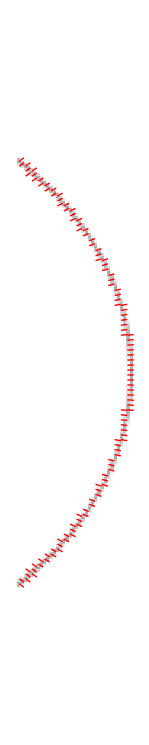

```mathematica
Print@@smp[[1]];
yPosXZSlice=Round[smp[[1,2,2]]/2];  (*Y position of X-Z slice*)
scaleLine=2;  (*1 draws a line every voxel, 2 every second voxel, etc.*)
lineList=DeleteCases[Flatten[Table[If[smp[[2,j,yPosXZSlice,i]]≠0,deltaLine=scaleLine Drop[smp[[3,j,yPosXZSlice,i]],{2}]/2;{{i-0.5,j-0.5}-deltaLine,{i-0.5,j-0.5}+deltaLine}],
			{i,1,smp[[1,2,1]],scaleLine},{j,1,smp[[1,2,3]],scaleLine}],1],Null];
Graphics[{Raster[Abs[smp[[2,All,yPosXZSlice,All]]/smp[[1,14]]/3-1]],Red,Map[Line,lineList]}]
```

```mathematica
Print@@smp[[1]];
Graphics3D[Raster3D[Abs[smp[[2]]/smp[[1,14]]],ColorFunction->"GrayLevelOpacity"],Boxed->False]
(*tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Graphics3D[{Red,Map[Line,tmp]},ImageSize->200]*)
```

Shell box {X,Y,Z}={38,243,243}, shell outer radius=120.5, shell inner radius=117.5, radius center displacement={2,0,0}, shell height=35, all in units of voxPitch=0.577778µm, Δn=-0.172

-Graphics3D-

#### Birefringent bundle, bundleBir[radius,length,Δn,theta,azim], radius and length of a straight bundle (cylinder), inclination angle theta and azimuth azim of the bundle axis. For theta = azim = 0, the bundle axis is parallel the y-axis. The bundle material is birefringent with an optic axis that is parallel to the bundle axis. The birefringence Δn can be positive or negative, and if Δn=0 the optic axis is {0,0,0}. Δn is the same for every fully occupied voxel of the membrane. The birefringence of voxels near the edge of the object can be fractions of Δn.

```mathematica
bundleBir::usage="bundleBir[radius,length,Δn,theta,azim], radius and length of a straight bundle (cylinder).For theta = azim = 0, the bundle axis is parallel the y-axis.
The bundle axis is inclined by theta away from the y-z plane and rotated by azim around the x-axis, both in radian.  
The bundle material is birefringent with an optic axis that is parallel to the bundle axis. The birefringence Δn can be positive or negative, and if Δn=0 the optic axis is {0,0,0}. 
Δn is the same for every fully occupied voxel of the membrane. The birefringence of voxels near the edge of the object can be fractions of Δn.";

bundleBir[radius_,length_,Δn_,theta_,azim_]:=
Module[{r,l,bAxis,rotTheta,rotAzim,smpRegion,smpBounds,rSize, ΔnArray,opticAxisArray},
r=(Round[radius]+0.5); (*the 0.5 puts the center of the bundle in the center of a voxel*)
l=(Round[length]+0.5);
rotTheta=RotationMatrix[theta,{0,0,1}];
rotAzim=RotationMatrix[azim,{1,0,0}];
bAxis={rotAzim.(rotTheta.{0,-l/2,0}),rotAzim.(rotTheta.{0,l/2,0})};
smpRegion=Region@Cylinder[bAxis,r];
smpBounds=RegionBounds[smpRegion];
rSize=Ceiling[(Transpose[smpBounds][[2]]-Transpose[smpBounds][[1]])];Do[If[EvenQ[rSize[[i]]],rSize[[i]]+=1],{i,3}];
ΔnArray=Reverse[ImageData[RegionImage[smpRegion,RegionBounds[smpRegion],RasterSize->rSize]]Δn,{1,2}];
opticAxisArray=Table[If[ΔnArray[[k,j,i]]≠0,Normalize[bAxis[[2]]],{0,0,0}],{k,rSize[[3]]},{j,rSize[[2]]},{i,rSize[[1]]}];
{{"Bundle box {X,Y,Z}=",rSize ,", radius=",r,", length=",l,", all in units of voxPitch=",voxPitch,"µm, birefringence=",Δn,", rotation theta=",theta,", rotation azim=",azim},ΔnArray,opticAxisArray}]
```

Graphics

```mathematica
?bundleBir
```

```mathematica
smp=bundleBir[2,6,-0.172,90°,0°];
Print@@smp[[1]];
Graphics3D[Raster3D[smp[[2]]/smp[[1,10]],ColorFunction->"GrayLevelOpacity"]]
tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Graphics3D[{Red,Map[Line,tmp]},ImageSize->200]
```

Bundle box {X,Y,Z}={7,5,5}, radius=2.5, length=6.5, all in units of voxPitch=0.247619µm, birefringence=-0.172, rotation theta=90 °, rotation azim=0

-Graphics3D-

-Graphics3D-

```mathematica
radius=2;
length=30;
azim=45;
incl=45;
r=(Round[radius/voxPitch]+0.5)voxPitch; (*the 0.5 puts the center of the bundle in the center of a voxel*)
l=(Round[length/voxPitch]+0.5)voxPitch;
rota=RotationMatrix[azim Degree,{1,0,0}];
roti=RotationMatrix[incl Degree,rota.{0,0,1}];
bAxis={roti.(rota.{0,-l/2,0}),roti.(rota.{0,l/2,0})};
bRegion=Region@Cylinder[bAxis,r];
bBounds=RegionBounds[bRegion]
Ceiling[(Transpose[bBounds][[2]]-Transpose[bBounds][[1]])/voxPitch]
Graphics3D[{{EdgeForm[White],Opacity[0.2,Yellow],Cuboid@@Transpose[bBounds]},Cylinder[bAxis,r]},Boxed->False]
```

{{-12.1252,12.1252},{-9.34421,9.34421},{-9.34421,9.34421}}

{98,76,76}

-Graphics3D-

#### Export images

```mathematica
SetDirectory["/Users/rudolfo/Desktop"];
```

```mathematica
Export["Shell8CrossSectWithLines.png",%];
```

### Composites Inserting several objects into a larger, rasterized volume

```mathematica
(*Each object in an objectList (oL) includes the object function and its “lower left” position (low {X,Y,Z} triplet in units of voxPitch) in the larger volume*)
(*Be aware that objects are likely not to be centered on a miicrolens.*)
(*However, if needed, one can use the displacement vector in the simulation cell to move the object volume objVolBir in increments of voxPitch*)

(*Preconfigures object assemblies*)
oL1={{{2,2,2},guvBir[3,1,0.1]}};
oL2={{{1,4,1},guvBir[3,1,0.1]},{{1,25,1},guvBir[3,1,0.2]}};  (*for oL2={{{1,2,1},guvBir[3,1,0.1]},{{1,20,1},guvBir[3,1,0.2]}}, the two GUVs are each centered on a microlens*)
oL2A={{{4,1,1},ballBir[1,-0.3,0°,0°]},{{1,1,13},guvBir[3,1,0.2]}};
oL2B={{{1,1,1},bundleBir[3,20,0.2,0°,135°]},{{1,1,1},bundleBir[3,20,0.1,0°,45°]}};
oL3={{{1,3,3},sheetBirStack[sheetBirList2]},{{14,1,1},bundleBir[3,20,0.1,0°,135°]},{{24,7,7},guvBir[3,1,0.2]}};
oL4={{{1,3,3},sheetBirStack[sheetBirList2]},{{14,1,1},bundleBir[3,20,0.05,0°,135°]},{{24,7,7},
		guvBir[3,1,0.2]},{{33,6,6},ballBir[3,0.1,0°,0°]}};
oL4B={{{1,3,3},sheetBirStack[sheetBirList2]},{{1,20,1},bundleBir[3,20,0.05,-45°,135°]},{{7,30,20},guvBir[3.5,1,0.2]},
		{{1,6,25},ballBir[3,0.1,45°,0°]}};
```

```mathematica
(*Building a single object volume*)
smp=oL2A;
smpDim=Table[smp[[i,2,2]]//Dimensions,{i,Length[smp]}];
SparseArray[Flatten[Table[Table[({k-1,j-1,i-1}+Reverse[smp[[n,1]]])->smp[[n,2,2,k,j,i]],{i,smpDim[[n,3]]},{j,smpDim[[n,2]]},{k,smpDim[[n,1]]}],{n,Length[smp]}]]];
SparseArray[Flatten[Table[Table[{({k-1,j-1,i-1,3}+Append[Reverse[smp[[n,1]]],0])->smp[[n,2,3,k,j,i,3]],({k-1,j-1,i-1,2}+Append[Reverse[smp[[n,1]]],0])->smp[[n,2,3,k,j,i,2]],({k-1,j-1,i-1,1}+Append[Reverse[smp[[n,1]]],0])->smp[[n,2,3,k,j,i,1]]},{i,smpDim[[n,3]]},{j,smpDim[[n,2]]},{k,smpDim[[n,1]]}],{n,Length[smp]}]]];
objVolBir={{"Object box {X,Y,Z}=",Reverse[Dimensions[%%]],", in units of voxPitch=",voxPitch,"µm"},%%,%};
```

```mathematica
(*Graphics for larger object volume*)
smp=objVolBir;
Print@@smp[[1]];
ΔnMax=Max[Abs[smp[[2]]]];
Graphics3D[Raster3D[Abs[smp[[2]]]/(ΔnMax),ColorFunction->"GrayLevelOpacity"],Axes->True,AxesLabel->{"X","Y","Z"}]
tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Graphics3D[{Red,Map[Line,tmp]},ImageSize->300]
```

Object box {X,Y,Z}={9,9,21}, in units of voxPitch=0.577778µm

-Graphics3D-

-Graphics3D-

```mathematica
SetDirectory["/Users/rudolfo/Desktop"]
```

/Users/rudolfo/Desktop

```mathematica
voxPitch
```

0.577778

```mathematica
Export["objVolBir_vP0.578.tiff",Image3D[objVolBir[[2]]]]
```

objVolBir_vP0.578.tiff

```mathematica
Dimensions[objVolBir[[2]]]
```

{9,48,9}

### Generator Code Open the grouped cells and generate a simulation by evaluating the Simulation Cell. To set up a new simulation, specify in the first two lines of the Simulation Cell: the object, e.g. smp=shellBir[15,10,1,0.1], the number of microlenses in horizontal and vertical direction, e.g. jjkkMinMax=Round[{-5,5,-5,5}], and the displacement of the object from the center, e.g. displace={0,0,0}. Then evaluate the Simulation Cell for generating the 4-dimensional Jones matrix array jM4DArray jM4DArray can be converted into light field images of the retardance and azimuth values, or into LC-PolScope intensity images, all using methods defined in the Initialization cell Note that all distances are made commensurate with the voxPitch

#### Mathematical expressions for the train of retardance Jones matrices, rayJM, defined for a given ray characterized by rayDir and object space voxels i that the ray traverses

rayDir specifies a ray
rayDir is a list of three 3D unit vectors, the first rayDir[1] points in the ray direction, 
the second and third vectors rayDir[2] and rayDir[3] span the plane perpendicular 
to the ray direction, all in object space. Furthermore, for each ray, rayDir[2] and 
rayDir[3] become parallel to the y-and z-axis, respectively, of the laboratory coordinate 
system, after the ray has passed through the objective lens, which rotates the ray 
direction parallel to the x-axis towards the camera. This is necessary for defining for 
all rays, regardless of their direction rayDir[1], a common 2D coordinate system in which 
the retardance is calculated that the rays are accumulating when passing through the 
series of voxels v. Accordingly, no further rotation of the coordinate system is required 
when applying the polarization components (polarizers and universal compensator) 
that are part of the microscope optical train and are typically placed between the 
objective lens and tube lens for computing the rays’ intensities after they have passed 
through those components.

birefringence Δn_v of voxel v
if Δn_v > 0  ⇒  azim_v(rayDir) = arctan(opticAxis_v . rayDir[2] , opticAxis_v . rayDir[3])
if Δn_v < 0  ⇒  azim_v(rayDir) = arctan(opticAxis_v . rayDir[2] , opticAxis_v . rayDir[3]) + 90° 
if Δn_v = 0 ⇒  azim_v(rayDir) = 0
azim_v(rayDir) is the angle of the slow axis of retardance, given in the laboratory x-y plane 
and experienced by a light ray traversing voxel v whose birefringence is Δn_v and optic axis 
orientation is given by the 3D unit vector opticAxis_v. 

opticAxis_v . rayDir[*] are dot or scalar products between vectors  opticAxis_v and rayDir[*],
representing the projection of one vector upon the direction of the other vector.

ret_v(rayDir) = |Δn_v| · (1 - (opticAxis_v . rayDir[1])^2) · (2π · l_v)/λ
ret_v(rayDir) is the retardance experienced by a light ray of wavelength λ and direction 
rayDir[1] when traversing voxel v whose birefringence is Δn_v and optic axis orientation 
is opticAxis_v.  l_v is the ray’s intersection length with the voxel. 

voxRayJM_v = (cos(ret_v/2)+i cos(2 azim_v) sin(ret_v/2) | i sin(2 azim_v) sin(ret_v/2)
i sin(2 azim_v) sin(ret_v/2) | cos(ret_v/2)- i cos(2 azim_v) sin(ret_v/2))
voxRayJM_v is the Jones matrix of voxel v with birefringence Δn_v and opticAxis_v, which translate 
into retardance ret_v and azimuth azim_v as calculated before.

rayJM = Π_v^LvoxRayJM_v
rayJM is the product of Jones matrices voxRayJM_v associated with the number L of voxels v 
that the ray traverses in the sample volume. (In Mathematica, to code the product of Jones 
matrices one needs to use Dot[].) In general, it is important that the sequence of Jones matrices 
corresponds to the sequence of the voxels that the ray traverses. However, for small retardance 
values ret_v (how small?), the Jones matrices commute and the exact sequence does not matter.

Two or more parallel rays that are focused into the same pixel of the light field camera are considered 
coherent and their Jones matrices are added, as suggested by the distributive law of products.

```mathematica
?ballBir
```

```mathematica
(*Simulation Cell*)

smp=ballBir[1,-0.172,45°,75°];jjkkMinMax=Round[{-2,2,-2,2}]; (*jjkkMinMax is the number of microlenses in y- and z-direction; the larger the object and the more it is out of focus the more microlenses*)
displace={0,0,0};(*displacement from voxNrCtr in units of voxPitch*)

Print@@smp[[1]];
subµLns=Floor[µLensPitch/(2voxPitch)];
thisRayEnter=Table[tmp=rayEnter[[i]]/voxPitch+(voxNrCtr[[1]]+(-smp[[1,2,1]]/2+displace[[1]]))/voxNrCtr[[1]](voxNrCtr-rayEnter[[i]]/voxPitch);{0,tmp[[2]],tmp[[3]]},{i,nrRays}];(*thisRayEnter is the list of {X,Y,Z} coordinates where rays enter into the Y-Z slice of object space that contains the sample object*)
thisRayExit=Table[tmp=rayEnter[[i]]/voxPitch+(voxNrCtr[[1]]+(smp[[1,2,1]]/2+displace[[1]]))/voxNrCtr[[1]](voxNrCtr-rayEnter[[i]]/voxPitch);{smp[[1,2,1]],tmp[[2]],tmp[[3]]},{i,nrRays}];
smpBoxNrs0=Transpose[{{0,voxNrCtr[[2]]-smp[[1,2,2]]/2,voxNrCtr[[3]]-smp[[1,2,3]]/2},{smp[[1,2,1]],voxNrCtr[[2]]+smp[[1,2,2]]/2,voxNrCtr[[3]]+smp[[1,2,3]]/2}}+Abs[displace[[1]]]{{0,-Tan[ArcSin[naObj/nMedium]],-Tan[ArcSin[naObj/nMedium]]},{0,Tan[ArcSin[naObj/nMedium]],Tan[ArcSin[naObj/nMedium]]}}]//Round;
smpBoxNrs=Transpose[{tmp1=voxNrCtr+displace-smp[[1,2]]/2;{0,tmp1[[2]],tmp1[[3]]},tmp2=voxNrCtr+displace+smp[[1,2]]/2;{smp[[1,2,1]],tmp2[[2]],tmp2[[3]]}}]//Round;
smpBoxNrsPrint=Transpose[{voxNrCtr+displace-smp[[1,2]]/2,voxNrCtr+displace+smp[[1,2]]/2}];
Print["sample box = ",smpBoxNrsPrint//N, " [voxPitch]"];
Timing[
	objectArray=ArrayPad[smp[[2]],Transpose[(Transpose[Reverse[smpBoxNrs]]-{{0,0,0},{voxNrYZ,voxNrYZ,smp[[1,2,1]]}}){1,-1}]];
	tmp4=.;objectArrayDipVec=ArrayPad[smp[[3]],Transpose[(Transpose[Reverse[smpBoxNrs]]-{{0,0,0},{voxNrYZ,voxNrYZ,smp[[1,2,1]]}}){1,-1}],tmp4]/.tmp4->{0,0,0};"seconds"
]
rayEnterCamPix=Table[camRayEntrance[[i,1]],{i,nrRays}]; (*List of {i,j} coordinates of camera pixels that correspond to rays that enter object space*)
mP0=Table[midPoints[thisRayEnter[[i]],thisRayExit[[i]],{1.,1.,1.},smpBoxNrs0],{i,nrRays}];(*list of midPoint lists for every ray within naObj centered on voxNrCtr; *)
iL=Table[intersectLength[thisRayEnter[[i]],thisRayExit[[i]],{1.,1.,1.},smpBoxNrs0]voxPitch,{i,nrRays}];(*list of intersectLength lists for every ray within naObj centered on voxNrCtr; this list remains the same even when the µLens is shifted in y- and z-direction*)
rayJM=Table[{{1,0},{0,1}},{i,nrCamPix},{j,nrCamPix}];
jM4DArray=Table[{{1,0},{0,1}},{jj,jjkkMinMax[[2]]-jjkkMinMax[[1]]+1},{kk,jjkkMinMax[[4]]-jjkkMinMax[[3]]+1}];
Timing[Monitor[
	Do[
		Do[mP0ii=Plus[#,{0,jj µLensPitch/voxPitch//Round,kk µLensPitch/voxPitch//Round}]&/@mP0[[ii]]; (*moving the midPoints by increments of µLensPitch*)
			rayJM[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]={{1,0},{0,1}};

			Do[mP=Plus[#,{0,jjj,kkk}]&/@mP0ii; (*moving the midPoints by increments of voxPitch within a µLensPitch*)
				tmp2=Ceiling[Reverse[mP,2]];  (*Reverse[mP,2] puts the part identifier in the right order [[k,j,i]]*)
				Δn=Extract[objectArray,tmp2];
				opticAxis=Extract[objectArrayDipVec,tmp2];
				(*Train of Dot products of linear retarder object voxels along ray path. The general linear retarder matrices of rays that arrive at the same camera pixel behind the µLens are added*)
				rayJM[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]+=(Dot@@Table[If[Δn[[i]]≠0,voxRayJM[Δn[[i]],opticAxis[[i]],rayUnitVectors[[ii]],iL[[ii,i]]],{{1,0},{0,1}}],{i,Length[iL[[ii]]]}]),
			{jjj,-subµLns,subµLns},{kkk,-subµLns,subµLns}],
		{ii,nrRays}];
		jjLF=jj-jjkkMinMax[[1]]+1;kkLF=kk-jjkkMinMax[[3]]+1;
		jM4DArray[[jjLF,kkLF]]=rayJM;,
	{jj,jjkkMinMax[[1]],jjkkMinMax[[2]]},{kk,jjkkMinMax[[3]],jjkkMinMax[[4]]}];"seconds",
ProgressIndicator[(jj-jjkkMinMax[[1]]+1)/(jjkkMinMax[[2]]-jjkkMinMax[[1]]+1)]]]
```

Ball box {X,Y,Z}={3,3,3}, radius=1.5, all in units of voxPitch=0.346667µm, birefringence=-0.172, rotation theta=45 °, rotation azim=75 °

sample box = {{359.5,362.5},{1008.5,1011.5},{1008.5,1011.5}} [voxPitch]

{4.23783,seconds}

{4.4606,seconds}

```mathematica
Map[jMRet,ArrayFlatten[Transpose[jM4DArray],2],{2}]//Raster//Graphics//ImageAdjust
```

-Graphics-

```mathematica
Map[jMRet,ArrayFlatten[Transpose[jM4DArray],2],{2}]2//Image
```

-Graphics-

```mathematica
Export["SimZ0.png",%]
```

SimZ0.png

```mathematica
SetDirectory["/Users/rudolfo/Desktop"];
```

```mathematica
Map[jMRet,ArrayFlatten[Transpose[jM4DArray],2],{2}]//Max
```

0.532145

```mathematica
Map[jMAzim,ArrayFlatten[Transpose[jM4DArray],2],{2}]//Raster//Graphics//ImageAdjust
```

-Graphics-

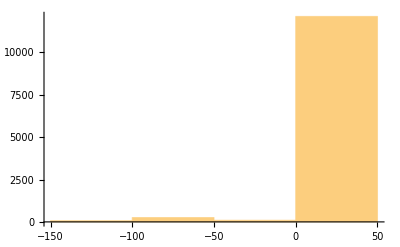

```mathematica
Histogram[Flatten[Map[jMAzim,ArrayFlatten[Transpose[jM4DArray],2],{2}]]180/Pi]
```

```mathematica
?showRetAndAzimLines
```

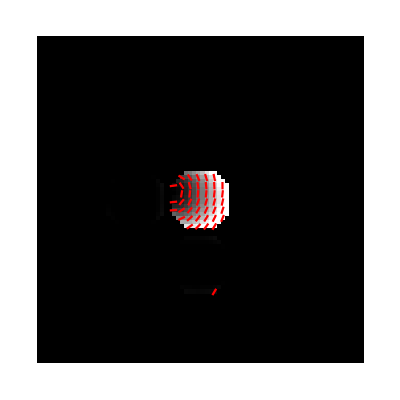

```mathematica
graphArray=jM4DArray;
(*graphArray=jM4DArray;*)
retList=Map[jMRet,ArrayFlatten[Transpose[graphArray],2],{2}];
azimList=Map[jMAzim,ArrayFlatten[Transpose[graphArray],2],{2}];
showRetAndAzimLines[{retList,azimList},{0,0.4},2,0.9,0.004,{1,1,1},0.017,400]
```

```mathematica
Export["SimZ+5.png",%]
```

SimZ+5.png

```mathematica
(*Saving a jM4DArray as a Mathematica expression*)
jM4DArray>>"jM4DArrayN18";
```

```mathematica
SetDirectory["/Users/rudolfo/Desktop"];
```

### Graphics for light field camera, object space, a complete Light Field LC-PolScope, and schematics for Figures in the article

#### Initialization

```mathematica
voxPitchGraphics=25;        (*voxel size for rendering graphics; it is typically much bigger than the simulation voxPitch*)
voxPitchGraphicsList={voxPitchGraphics,voxPitchGraphics,voxPitchGraphics};
If[OddQ[voxNrXGraphics=Round[250/voxPitchGraphics]],,voxNrXGraphics=voxNrXGraphics+1]; (*voxNrXGraphics is the number of voxels along the x-axis side of the object cube. An odd number will put the Center of a voxel in the center of object space*)
If[OddQ[voxNrYZGraphics=Round[700/voxPitchGraphics]],,voxNrYZGraphics=voxNrYZGraphics+1]; (*voxNrYZGraphics is the number of voxels along the y- and z-axis side of the object cube An odd number will put the Center of a voxel in the center of object space*)
voxNrCtrGraphics={voxNrXGraphics/2,voxNrYZGraphics/2,voxNrYZGraphics/2};(*voxNrCtrGraphics is the number location in object space on which all camera rays converge*)
volCtrGraphics={voxNrXGraphics*voxPitchGraphics/2,voxNrYZGraphics*voxPitchGraphics/2,voxNrYZGraphics*voxPitchGraphics/2};(*volCtr is the center of the sample volume and the location in object space on which all rays of the central microlens converge*)

voxPitch=µLensPitch/5;voxPitch::usage="voxPitch is the side length in micron of a cubic voxel in object space;\nyou can change it to voxPitch=µLensPitch/1, or voxPitch=µLensPitch/3, voxPitch=µLensPitch/5";
λ=0.550; wavelength::usage="λ is the wavelength in µm of light propagating through the sample volume.\nIt is used to convert retardance given as Δn times the ray's path length into a phase angle and vice versa";
If[OddQ[voxNrX=Round[250/voxPitch]],,voxNrX=voxNrX+1]; voxNrX::usage="voxNrX is the number of voxels along the x-axis side of the object cube.\nAn odd number will put the Center of a voxel in the center of object space";
If[OddQ[voxNrYZ=Round[700/voxPitch]],,voxNrYZ=voxNrYZ+1]; voxNrYZ::usage="voxNrYZ is the number of voxels along the y- and z-axis side of the object cube\nAn odd number will put the Center of a voxel in the center of object space";
voxNrCtr={voxNrX/2,voxNrYZ/2,voxNrYZ/2};voxNrCtr::usage="voxNrCtr is the number location in object space on which all camera rays converge";
volCtr={voxNrX*voxPitch/2,voxNrYZ*voxPitch/2,voxNrYZ*voxPitch/2};volCtr::usage="volCtr is the center of the sample volume in µm and the location in object space on which all rays of the central microlens converge";
magnObj=60;  magnObj::usage="magnObj is the magnification of objective lens";
µLensCtr={8,8}; µLensCtr::usage="µLensCtr is the microLens center position in camera pixels";
µLensPitch=nrCamPix*camPixPitch/magnObj;  µLensPitch::usage="µLens pitch in object space is about 1.733µm when using 60x objective lens.\n1.733*60=104µm is actually a bit bigger than 100µm pitch of the experimental µLens array.\n104µm makes it an integer number of camera pixels.";
rNA =7.5;  rNA::usage="rNA is the radius of the edge of the objective lens aperture in camera pixels; rNA = 7.5 for 60x/1.4NA objective lens and a condenser NA of 1.2";
nrCamPix=16;  nrCamPix::usage="nrCamPix is the number of camera pixels behind a lenslet in the horizontal and vertical direction\n0≤i≤nrCamPix and 0≤j≤nrCamPix span the plane of camera pixels, with {i,j} Reals\nIntegers {i,j} count the pixels. {0.5,0.5} is the center location of pixel {1,1}";
camPixPitch=6.5;  camPixPitch::usage="camPixPitch is the size of the camera pixels in µm in image space";
naObj=1.2;     naObj::usage="naObj is NA of objective lens";
nMedium=1.52;  nMedium::usage="nMedium is the refractive index of the medium in object space";

(*The computation implements the Abbe sine condition for points in the back focal plane of the objective lens*)
(*Making this a delayed assignment slows down the computation tremendously*)
(*Angle values need to be converted and rounded to integer degrees, otherwise later the test for all members of mP and iL having equal length fails for all voxPitch values. I don't know why!*)
camPixRays::usage="The list camPixRays[[i,j]] holds values for azimuth and tilt angles in object space for rays originating in camera pixels {i,j} behind the central lenslet";
camPixRays=Table[If[(tmp=Sqrt[(i-0.5-µLensCtr[[1]])^2+(j-0.5-µLensCtr[[2]])^2])>rNA,{Null},
	{ArcTan[i-0.5-µLensCtr[[1]],j-0.5-µLensCtr[[2]]]/Degree,ArcSin[tmp/rNA*naObj/nMedium]/Degree}//Round],{i,nrCamPix},{j,nrCamPix}];

(*2D line grid representing camera pixel array behind one microlens*)
camPixels2D:={
	Table[Line[{{1,0}*i,{1,0}*i+{0,1}*nrCamPix}],{i,0,nrCamPix}],
	Table[Line[{{0,1}*i,{0,1}*i+{1,0}*nrCamPix}],{i,0,nrCamPix}],
	Table[Text[{i,j},{(i-0.5),(j-0.5)}],{i,nrCamPix},{j,nrCamPix}]
}

camRayEntrance::usage="The camRayEntrance list holds the positions where camera rays originating in pixel {i,j} pass through the entrance face into the object cube.\nThe x position of the entrance face is 0, camera rays all converge on volCtr";
camRayEntrance:=Flatten[Table[If[camPixRays[[i,j]]=={Null},,{{i,j},
		{0,volCtr[[1]]*Tan[camPixRays[[i,j,2]]Degree]Sin[camPixRays[[i,j,1]]Degree]+volCtr[[2]],
		volCtr[[1]]*Tan[camPixRays[[i,j,2]]Degree]Cos[camPixRays[[i,j,1]]Degree]+volCtr[[3]]}}],{i,nrCamPix},{j,nrCamPix}]//N,1]//DeleteCases[Null]

nrRays=Length[camRayEntrance]; nrRays::usage="nrRays is the  number of all rays (172 for naObj=1.2 and rNA=7.5; 188 for naObj=1.2 and rNA=7.7) that fall onto the camera and pass through the objective aperture";

rayEnter::usage="List of object space coordinates where rays enter object space. The x-position is 0";
rayEnter=Table[camRayEntrance[[i,2]],{i,nrRays}];

rayExit::usage="List of object space coordinates where rays exit object space. The x-position is voxPitch*voxNrX";
rayExit=Table[rayEnter[[i]]+2(volCtr-rayEnter[[i]]),{i,nrRays}];

(*The camRayEntrance list holds the positions where camera rays originating in pixel {i,j} pass through the entrance face into the object cube or vice versa.\nThe x position of the entrance face is 0, camera rays all converge on volCtr*)
camRayEntranceGraphics::usage="The camRayEntranceGraphics list holds the positions where camera rays originating in pixel {i,j} pass through the entrance face into the object cube or vice versa.\nThe x position of the entrance face is 0, camera rays all converge on volCtr.\nDistances computed with Graphicsics related units (voxPitchGraphics, volCtrGraphics)";
camRayEntranceGraphics:=Flatten[Table[If[camPixRays[[i,j]]=={Null},,{{i,j},
		{0,volCtrGraphics[[1]]*Tan[camPixRays[[i,j,2]]Degree]Sin[camPixRays[[i,j,1]]Degree]+volCtrGraphics[[2]],
		volCtrGraphics[[1]]*Tan[camPixRays[[i,j,2]]Degree]Cos[camPixRays[[i,j,1]]Degree]+volCtrGraphics[[3]]}}],{i,nrCamPix},{j,nrCamPix}]//N,1]//DeleteCases[Null]

(*The entrance face is where rays enter object space. The face is in the y-z plane at x=0.\nDistances computed with Graphics related units (voxPitchGraphics,voxNrYZGraphics)*)
entranceFaceGraphics:={
	Table[Line[{{0,1,0}*voxPitchGraphics*i,{0,1,0}*voxPitchGraphics*i+{0,0,1}*voxPitchGraphics*voxNrYZGraphics}],{i,0,voxNrYZGraphics}],
	Table[Line[{{0,0,1}*voxPitchGraphics*i,{0,0,1}*voxPitchGraphics*i+{0,1,0}*voxPitchGraphics*voxNrYZGraphics}],{i,0,voxNrYZGraphics}]
}

(*2D line grid representing entrance face of rays that traverse object space.\nDistances computed with Graphics related units (voxPitchGraphics,voxNrYZGraphics)*)
entranceFace2DGraphics:={
	Table[Line[{{1,0}*voxPitchGraphics*i,{1,0}*voxPitchGraphics*i+{0,1}*voxPitchGraphics*voxNrYZGraphics}],{i,0,voxNrYZGraphics}],
	Table[Line[{{0,1}*voxPitchGraphics*i,{0,1}*voxPitchGraphics*i+{1,0}*voxPitchGraphics*voxNrYZGraphics}],{i,0,voxNrYZGraphics}]
}

(*The exit face is where rays exit object space. The face is in the y-z plane at x=voxNrXGraphics·voxPitchGraph*)
exitFaceGraphics:={
	Table[Line[{{0,1,0}*voxPitchGraphics*i+{1,0,0}*voxPitchGraphics*voxNrXGraphics,{0,1,0}*voxPitchGraphics*i+{0,0,1}*voxPitchGraphics*voxNrYZGraphics+{1,0,0}*voxPitchGraphics*voxNrXGraphics}],{i,0,voxNrYZGraphics}],
	Table[Line[{{0,0,1}*voxPitchGraphics*i+{1,0,0}*voxPitchGraphics*voxNrXGraphics,{0,0,1}*voxPitchGraphics*i+{0,1,0}*voxPitchGraphics*voxNrYZGraphics+{1,0,0}*voxPitchGraphics*voxNrXGraphics}],{i,0,voxNrYZGraphics}]
}

(*object cube.\nDistances computed with Graphics related units (voxPitchGraphics,voxNrxGraphics,voxNrYZGraphics)*)
objectCubeGraphics:={
	Table[Line[{{0,1,0}*voxPitchGraphics*i+{1,0,0}*voxPitchGraphics*j,{0,1,0}*voxPitchGraphics*i+{0,0,1}*voxPitchGraphics*voxNrYZGraphics+{1,0,0}*voxPitchGraphics*j}],{i,0,voxNrYZGraphics},{j,voxNrXGraphics-1}],
	Table[Line[{{0,0,1}*voxPitchGraphics*i+{1,0,0}*voxPitchGraphics*j,{0,0,1}*voxPitchGraphics*i+{0,1,0}*voxPitchGraphics*voxNrYZGraphics+{1,0,0}*voxPitchGraphics*j}],{i,0,voxNrYZGraphics},{j,voxNrXGraphics-1}],
	Table[Line[{{0,0,1}*voxPitchGraphics*i+{0,1,0}*voxPitchGraphics*j,{0,0,1}*voxPitchGraphics*i+{0,1,0}*voxPitchGraphics*j+{1,0,0}*voxPitchGraphics*voxNrXGraphics}],{i,0,voxNrYZGraphics},{j,0,voxNrYZGraphics}]
}

(*Siddon algorithms, Mathematica implementation by Rudolf Oldenbourg, March 2019, based on Python code from Nathaniel Holderman, UChicago, in 2018*)
(*pixNumXIn is the number of voxels in x-direction between entrance face and front face of bounding object box. The same applies to y- and z-direction*)
(*pixNumXOut is the number of voxels in x-direction between entrance face and back face of bounding object box. The same applies to y- and z-direction*)
(*dx_,dy_, and dz_ must be Real numbers, not integers*)
rayTrace[{x1_,y1_,z1_},{x2_,y2_,z2_},{dx_,dy_,dz_},{{pixNumXIn_,pixNumXOut_},{pixNumYIn_,pixNumYOut_},{pixNumZIn_,pixNumZOut_}}]:=
(*Catch[*)Module[{ax={},ax0,axN,ay={},ay0,ayN,az={},az0,azN,aMin,aMax,iMin,iMax,jMin,jMax,kMin,kMax},
(*first,compute starting and ending parametric values in each dimension*)
		If[x2-x1≠0,ax0=(pixNumXIn dx-x1)/(x2-x1);axN=(pixNumXOut*dx-x1)/(x2-x1),ax0=0.;axN=1.];
		If[y2-y1≠0,ay0=(pixNumYIn dy-y1)/(y2-y1);ayN=(pixNumYOut*dy-y1)/(y2-y1),ay0=0.;ayN=1.];
		If[z2-z1≠0,az0=(pixNumZIn dz-z1)/(z2-z1);azN=(pixNumZOut*dz-z1)/(z2-z1),az0=0.;azN=1.];
(*Print["ax0=",ax0,", axN=",axN,", ay0=",ay0,", ayN=",ayN,", az0=",az0,", azN=",azN];*)
(*then calculate absolute max and min parametric values*)
		aMin=Max[0.,Min[ax0,axN],Min[ay0,ayN],Min[az0,azN]];
		aMax=Min[1.,Max[ax0,axN],Max[ay0,ayN],Max[az0,azN]];
(*Print["aMin=",aMin,", aMax=",aMax];*)
(*now find range of indices corresponding to max/min a values*)
(*in this application, (x2-x1) is always greater zero*)
(*		iMin=Ceiling[(aMin*(x2-x1)-x1)/dx];iMax=Floor[1+(x1+aMax*(x2-x1))/dx];*)
		iMin=Ceiling[pixNumXOut-(pixNumXOut*dx-aMin*(x2-x1)-x1)/dx];iMax=Floor[1+(x1+aMax*(x2-x1))/dx];
		If[(y2-y1)≥0,
			jMin=Ceiling[pixNumYOut-(pixNumYOut*dy-aMin*(y2-y1)-y1)/dy];jMax=Floor[1+(y1+aMax*(y2-y1))/dy],
			jMin=Ceiling[pixNumYOut-(pixNumYOut*dy-aMax*(y2-y1)-y1)/dy];jMax=Floor[1+(y1+aMin*(y2-y1))/dy]];
		If[(z2-z1)≥0,
			kMin=Ceiling[pixNumZOut-(pixNumZOut*dz-aMin*(z2-z1)-z1)/dz];kMax=Floor[1+(z1+aMax*(z2-z1))/dz],
			kMin=Ceiling[pixNumZOut-(pixNumZOut*dz-aMax*(z2-z1)-z1)/dz];kMax=Floor[1+(z1+aMin*(z2-z1))/dz]];
(*Print["iMin=",iMin,", iMax=",iMax,", jMin=",jMin,", jMax=",jMax,", kMin=",kMin,", kMax=",kMax];*)
(*next calculate the list of parametric values for each coordinate*)
		For [i=iMin,i<iMax,i++,ax=Append[ax,(i*dx-x1)/(x2-x1)]];
		If [y2-y1>0,For [j=jMin,j<jMax,j++,ay=Append[ay,(j*dy-y1)/(y2-y1)]]];
		If [y2-y1<0,For [j=jMin,j<jMax,j++,ay=Prepend[ay,(j*dy-y1)/(y2-y1)]]];
		If [z2-z1>0,For [k=kMin,k<kMax,k++,az=Append[az,(k*dz-z1)/(z2-z1)]]];
		If [z2-z1<0,For [k=kMin,k<kMax,k++,az=Prepend[az,(k*dz-z1)/(z2-z1)]]];
(*Print["ax=",ax];
Print["ay=",ay];
Print["az=",az];
Throw["thrown"];*)
(*finally,form the list of parametric values*)
		Union[{aMin},ax,ay,az,{aMax}]]
(*	]*)

midPoints[{x1_,y1_,z1_},{x2_,y2_,z2_},{dx_,dy_,dz_},{{pixNumXIn_,pixNumXOut_},{pixNumYIn_,pixNumYOut_},{pixNumZIn_,pixNumZOut_}}]:=
	Module[{aList,x,y,z,iMid},
		aList=rayTrace[{x1,y1,z1},{x2,y2,z2},{dx,dy,dz},{{pixNumXIn,pixNumXOut},{pixNumYIn,pixNumYOut},{pixNumZIn,pixNumZOut}}];
(*loop through, computing midpoints for each adjacent pair of a values for chosen coord*)
		iMid={};
		For[m =2,m≤Length[aList],m++,
			x=.5*(aList[[m]]+aList[[m-1]])*(x2-x1)+x1;
			y=.5*(aList[[m]]+aList[[m-1]])*(y2-y1)+y1;
			z=.5*(aList[[m]]+aList[[m-1]])*(z2-z1)+z1;
			iMid=Append[iMid,{x,y,z}]];
	iMid]

intersectLength[{x1_,y1_,z1_},{x2_,y2_,z2_},{dx_,dy_,dz_},{{pixNumXIn_,pixNumXOut_},{pixNumYIn_,pixNumYOut_},{pixNumZIn_,pixNumZOut_}}]:=
	Module[{aList,lengths},
		aList=rayTrace[{x1,y1,z1},{x2,y2,z2},{dx,dy,dz},{{pixNumXIn,pixNumXOut},{pixNumYIn,pixNumYOut},{pixNumZIn,pixNumZOut}}];
(*find length of intersection by multiplying difference in parametric values by total ray length*)
		lengths={};
		For[m =2,m≤Length[aList],m++,
			lengths=Append[lengths,Sqrt[(x2-x1)^2+(y2-y1)^2+(z2-z1)^2]*(aList[[m]]-aList[[m-1]])]];
	lengths]
```

Light field microscope components

```mathematica
fontSizeParameter=18;
```

```mathematica
lfSensor[zPosition_,opacity_]:=Show[{Graphics3D[{GrayLevel[.75],Opacity[opacity],Specularity[White,50],pixPitchG=0.6;
		Table[Cuboid[{i-pixPitchG/2,j-pixPitchG/2,-0.2+zPosition+1.5},{i+pixPitchG/2,j+0.1pixPitchG/2,0.02+zPosition+1.5}],{i,-7.2,7.2,pixPitchG},{j,-7.2,7.2,pixPitchG}]}],
	Table[ParametricPlot3D[{i+1.8Cos[u]Sin[v],j+ 1.8Sin[u]Sin[v],0.1+1.8(-Pi/4+Cos[v])+zPosition-1.5},{u,0,2Pi},{v,0,Pi/4},
		PlotStyle->{GrayLevel[.5],Opacity[opacity/3],Specularity[White,50]},Mesh->None],{i,-6,6,2},{j,-6,6,2}],
	Graphics3D[{GrayLevel[.5],Opacity[opacity],Specularity[White,50],
		Cuboid[{-7.3,-7.3,-0.2+zPosition-1.5},{7.3,7.3,zPosition-1.5}],
		Opacity[1],Black,Thick,
		Line[{{-12.5,0,zPosition+3},{-13,0,zPosition+2.5},{-13,0,zPosition+0.5},{-13.5,0,zPosition}}],
		Line[{{-12.5,0,zPosition-3},{-13,0,zPosition-2.5},{-13,0,zPosition-0.5},{-13.5,0,zPosition}}],
		Thin,Line[{{-13,0,zPosition},{-22,0,zPosition}}],
		Text[Style["Light Field Sensor",FontFamily->"Arial",FontSize->fontSizeParameter],{-23,0,zPosition},{1,0}]}]},
	PlotRange->{{-35,8},{-8,8},{zPosition-3,zPosition+3}},Lighting->"Neutral"]
```

```mathematica
lfSensor[zPosition_,opacity_,name_]:=Show[{Graphics3D[{GrayLevel[.75],Opacity[opacity],Specularity[White,50],pixPitchG=0.6;
		Table[Cuboid[{i-pixPitchG/2,j-pixPitchG/2,-0.2+zPosition+1.5},{i+pixPitchG/2,j+pixPitchG/2,0.02+zPosition+1.5}],{i,-7.2,7.2,pixPitchG},{j,-7.2,7.2,pixPitchG}]}],
	Table[ParametricPlot3D[{i+1.8Cos[u]Sin[v],j+ 1.8Sin[u]Sin[v],0.1+1.8(-Pi/4+Cos[v])+zPosition-1.5},{u,0,2Pi},{v,0,Pi/4},
		PlotStyle->{GrayLevel[.5],Opacity[opacity/3],Specularity[White,50]},Mesh->None],{i,-6,6,2},{j,-6,6,2}],
	Graphics3D[{GrayLevel[.5],Opacity[opacity],Specularity[White,50],
		Cuboid[{-7.3,-7.3,-0.2+zPosition-1.5},{7.3,7.3,zPosition-1.5}],
		If[name≠"NoName",{Opacity[1],Black,Thick,tmp={-2,0,0};
			Line[{{-8.5,0,zPosition+2}+tmp,{-9,0,zPosition+1.5}+tmp,{-9,0,zPosition+0.5}+tmp,{-9.5,0,zPosition}+tmp}],
			Line[{{-8.5,0,zPosition-2}+tmp,{-9,0,zPosition-1.5}+tmp,{-9,0,zPosition-0.5}+tmp,{-9.5,0,zPosition}+tmp}],
			Thin,Line[{{-13,0,zPosition},{-22,0,zPosition}}],
			Text[Style[name,FontFamily->"Arial",FontSize->fontSizeParameter],{-23,0,zPosition},{1,0}]}]}]},
	PlotRange->{If[name=="NoName",{-10,8},{-38,8}],{-8,8},{zPosition-3,zPosition+3}},Lighting->"Neutral"]
```

```mathematica
tubeLens[zPosition_,opacity_,name_]:=Module[{lensRadius=15},Show[{
		ParametricPlot3D[{lensRadius Cos[u]Sin[v],lensRadius Sin[u]Sin[v],zPosition+lensRadius( Cos[v]-0.87)},{u,0,2Pi},{v,0,Pi/6},
				PlotStyle->{GrayLevel[.5],Opacity[opacity],Specularity[White,50],Lighting->"Neutral"},Mesh->None],
		ParametricPlot3D[{lensRadius Cos[u]Sin[v],lensRadius Sin[u]Sin[v],zPosition+lensRadius( Cos[v]+0.87)},{u,0,2Pi},{v,5Pi/6,Pi},
				PlotStyle->{GrayLevel[.5],Opacity[opacity],Specularity[White,50],Lighting->"Neutral"},Mesh->None],
		If[name≠"NoName",
		Graphics3D[{Opacity[1],Black,Thin,Line[{{-13,0,zPosition},{-22,0,zPosition}}],
				Text[Style[name,FontFamily->"Arial",FontSize->fontSizeParameter],{-23,0,zPosition},{1,0}]}],Nothing]},
	Axes->False,
	PlotRange->{If[name=="NoName",{-8,8},{-35,8}],{-8,8},{zPosition-2,zPosition+2}},Lighting->"Neutral"]]
```

```mathematica
tubeLens[0,0.5,"Tube Lens"]
```

-Graphics3D-

```mathematica
(*left circular polarizer from the point of view of the receiver*)
(*the electric field vector rotates counterclockwise as it propagates towards the receiver*)
leftCircPolar[zPosition_,coloration_,opacity_,name_]:=Graphics3D[{coloration,Opacity[opacity],Specularity[White,50],EdgeForm[Gray],
		Cylinder[{{0,0,zPosition-0.2},{0,0,zPosition+0.2}},6],
		Opacity[1],Black,Thick,Line[Table[{5Cos[i],5Sin[i],zPosition+0.21},{i,-Pi/2,0,Pi/50}]],
		Line[{{5Cos[0],5Sin[0],zPosition+0.21},{5Cos[0]-1,5Sin[0]-1,zPosition+0.21}}],
		Line[{{5Cos[0],5Sin[0],zPosition+0.21},{5Cos[0]+0.5,5Sin[0]-1.5,zPosition+0.21}}],
		Thin,Line[{{-13,0,zPosition},{-22,0,zPosition}}],
		Text[Style[name,FontFamily->"Arial",FontSize->fontSizeParameter,FontColor->Black],{-23,0,zPosition},{1,0}]},
		PlotRange->{{-35,8},{-8,8},{zPosition-2,zPosition+2}},Lighting->"Neutral"]
```

```mathematica
objectiveLens[zPosition_,opacity_]:=Module[{lensRadius=6},Show[{
		ParametricPlot3D[{lensRadius Cos[u]Sin[v],lensRadius Sin[u]Sin[v],zPosition+lensRadius Cos[v]},{u,0,2Pi},{v,0,Pi/2},
			PlotStyle->{GrayLevel[.5],Opacity[opacity],Specularity[White,50],Lighting->"Neutral"},Mesh->None],
		ParametricPlot3D[{lensRadius Cos[u]Sin[v],lensRadius Sin[u]Sin[v],zPosition},{u,0,2Pi},{v,0,Pi/2},
			PlotStyle->{GrayLevel[.5],Opacity[opacity],Specularity[White,50],Lighting->"Neutral"},Mesh->None],
		Graphics3D[{Opacity[1],Black,Thin,Line[{{-13,0,zPosition+4},{-22,0,zPosition+4}}],
				Text[Style["Objective Lens",FontFamily->"Arial",FontSize->fontSizeParameter],{-23,0,zPosition+4},{1,0}]}]},
	Axes->False,
	PlotRange->{{-40,8},{-8,8},{zPosition-2,zPosition+6}},Lighting->"Neutral"]]
```

```mathematica
slideCoverslipSample[zPosition_,opacity_]:= Graphics3D[{GrayLevel[.75],Opacity[opacity], Specularity[White, 50],
		Cuboid[{-12, -6, -0.2 + zPosition}, {12, 6, 0.02 + zPosition}],
		Cuboid[{-5, -5,1.3 + zPosition}, {5, 5, 1.14 + zPosition}],
		Cuboid[{-5, -5,1.14 + zPosition}, {5, 5, 0 + zPosition}],
		(*Black,asterSectionObject/.zPosObject->zPosition,*)
		Style[Sphere[{0,0,zPosition}],Opacity[0.5],ClipPlanes->InfinitePlane[{{1,-1,zPosition},{1,1,zPosition},{0,0,zPosition}}]],
		Opacity[1],Black, Thin, Line[{{-13, 0, zPosition}, {-22, 0, zPosition}}],
		Text[Style["Sample", FontFamily -> "Arial", FontSize -> fontSizeParameter], {-23, 0, zPosition}, {1, 0}]},
		PlotRange -> {{-35, 13}, {-8, 8}, {zPosition - 2, zPosition + 2}}, Lighting -> "Neutral"]
```

```mathematica
condenserLens[zPosition_,opacity_]:=Module[{lensRadius=6},Show[{
		ParametricPlot3D[{lensRadius Cos[u]Sin[v],lensRadius Sin[u]Sin[v],zPosition+lensRadius Cos[v]},{u,0,2Pi},{v,Pi/2,Pi},
			PlotStyle->{GrayLevel[1],Opacity[opacity],Specularity[White,50],Lighting->"Neutral"},Mesh->None],
		ParametricPlot3D[{lensRadius Cos[u]Sin[v],lensRadius Sin[u]Sin[v],zPosition},{u,0,2Pi},{v,0,Pi/2},
			PlotStyle->{GrayLevel[.5],Opacity[opacity],Specularity[White,50],Lighting->"Neutral"},Mesh->None],
		Graphics3D[{Opacity[1],Black,Thin,Line[{{-13,0,zPosition-4},{-22,0,zPosition-4}}],
				Text[Style["Condenser Lens",FontFamily->"Arial",FontSize->fontSizeParameter],{-23,0,zPosition-4},{1,0}]}]},
	Axes->False,
	PlotRange->{{-40,8},{-8,8},{zPosition-6,zPosition+2}},Lighting->"Neutral"]]
```

```mathematica
lcCompensatorBonded[zPosition_,coloration_,opacity_,name_]:=Graphics3D[{coloration,Opacity[opacity],Specularity[White,50],
		Cuboid[{-6,-6,zPosition+0.5},{6,6,zPosition+0.9}],
		Cuboid[{-6,-6,zPosition},{6,6,zPosition+0.4}],
		Cylinder[{{0,0,zPosition-0.5},{0,0,zPosition-0.1}},6],
		Opacity[1],Black,Thick,Line[{{-6,0,zPosition-0.5},{6,0,zPosition-0.5}}],
		Thin,Line[{{-13,0,zPosition},{-22,0,zPosition}}],
		Text[Style[name,FontFamily->"Arial",FontSize->fontSizeParameter,FontColor->Black],{-23,0,zPosition},{1,0}]},
		PlotRange->{{-43,10},{-10,10},{zPosition-7,zPosition+4}},Lighting->"Neutral"]
```

```mathematica
ifFilter[zPosition_,coloration_,opacity_,name_]:=Graphics3D[{coloration,Opacity[opacity],Specularity[White,50],
		Cylinder[{{0,0,zPosition-0.2},{0,0,zPosition+0.2}},6],
		Opacity[1],Black,Thin,Line[{{-13,0,zPosition},{-22,0,zPosition}}],
		Text[Style[name,FontFamily->"Arial",FontSize->fontSizeParameter,FontColor->Black],{-23,0,zPosition},{1,0}]},
	PlotRange->{{-45,10},{-10,8},{zPosition-7,zPosition+4}},Lighting->"Neutral"]
```

```mathematica
collectorLens[zPosition_,opacity_]:=Module[{lensRadius=15},Show[{
		ParametricPlot3D[{lensRadius Cos[u]Sin[v],lensRadius Sin[u]Sin[v],zPosition+lensRadius( Cos[v]-0.87)},{u,0,2Pi},{v,0,Pi/6},
				PlotStyle->{GrayLevel[.5],Opacity[opacity],Specularity[White,50],Lighting->"Neutral"},Mesh->None],
		ParametricPlot3D[{lensRadius Cos[u]Sin[v],lensRadius Sin[u]Sin[v],zPosition+lensRadius( Cos[v]+0.87)},{u,0,2Pi},{v,5Pi/6,Pi},
				PlotStyle->{GrayLevel[.5],Opacity[opacity],Specularity[White,50],Lighting->"Neutral"},Mesh->None],
		Graphics3D[{Opacity[1],Black,Thin,Line[{{-13,0,zPosition},{-22,0,zPosition}}],
				Text[Style["Collector Lens",FontFamily->"Arial",FontSize->fontSizeParameter],{-23,0,zPosition},{1,0}]}]},
	Axes->False,
	PlotRange->{{-35,8},{-8,8},{zPosition-2,zPosition+2}},Lighting->"Neutral"]]
```

```mathematica
bulb2[zPosition_,opacity_]:=Graphics3D[{GrayLevel[.75],Opacity[opacity],Specularity[White,50],
		Cylinder[{{-6,0,zPosition},{-2.5,0,zPosition}},1.5],
		Sphere[{0,0,zPosition},3],
		GrayLevel[0],Opacity[1],
		Cylinder[{{-7,-0.5,zPosition},{-1,-0.5,zPosition}},0.2],
		Cylinder[{{-1,-0.5,zPosition},{0,-2,zPosition}},0.1],
		Cylinder[{{0,-2,zPosition},{0,2,zPosition}},0.4],
		Cylinder[{{-1,0.5,zPosition},{0,2,zPosition}},0.1],
		Cylinder[{{-7,0.5,zPosition},{-1,0.5,zPosition}},0.2],
		Opacity[1],Black,Thin,Line[{{-13,0,zPosition},{-22,0,zPosition}}],
		Text[Style["Light Source",FontFamily->"Arial",FontSize->fontSizeParameter],{-23,0,zPosition},{1,0}]},
		PlotRange->{{-40,10},{-10,8},{zPosition-7,zPosition+4}},Lighting->"Neutral"]
```

#### Camera pixel array and aperture disk

This graphics illustrates the 16 x 16 sensor pixels behind a single microlens and, in light blue, the microscope objective back aperture projected by the microlens

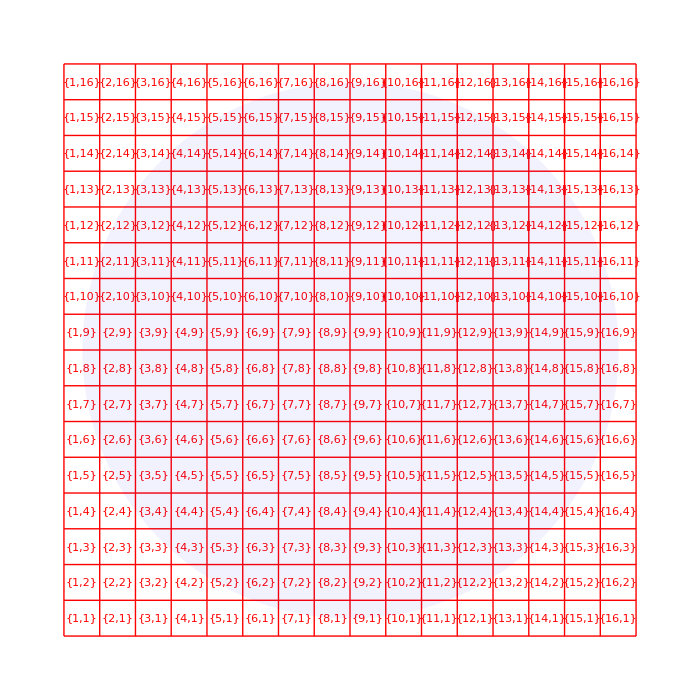

```mathematica
Graphics[{Red,camPixels2D,Blue,Opacity[0.05],Disk[µLensCtr,rNA]},ImageSize->700]
```

#### Ray positions in entrance face of object space for a single, centrally located microlens

The light blue disk indicates the range of possible positions of rays that pass through the center of object space and through the aperture of the microscope objective lens.

voxPitchGraphics = 25

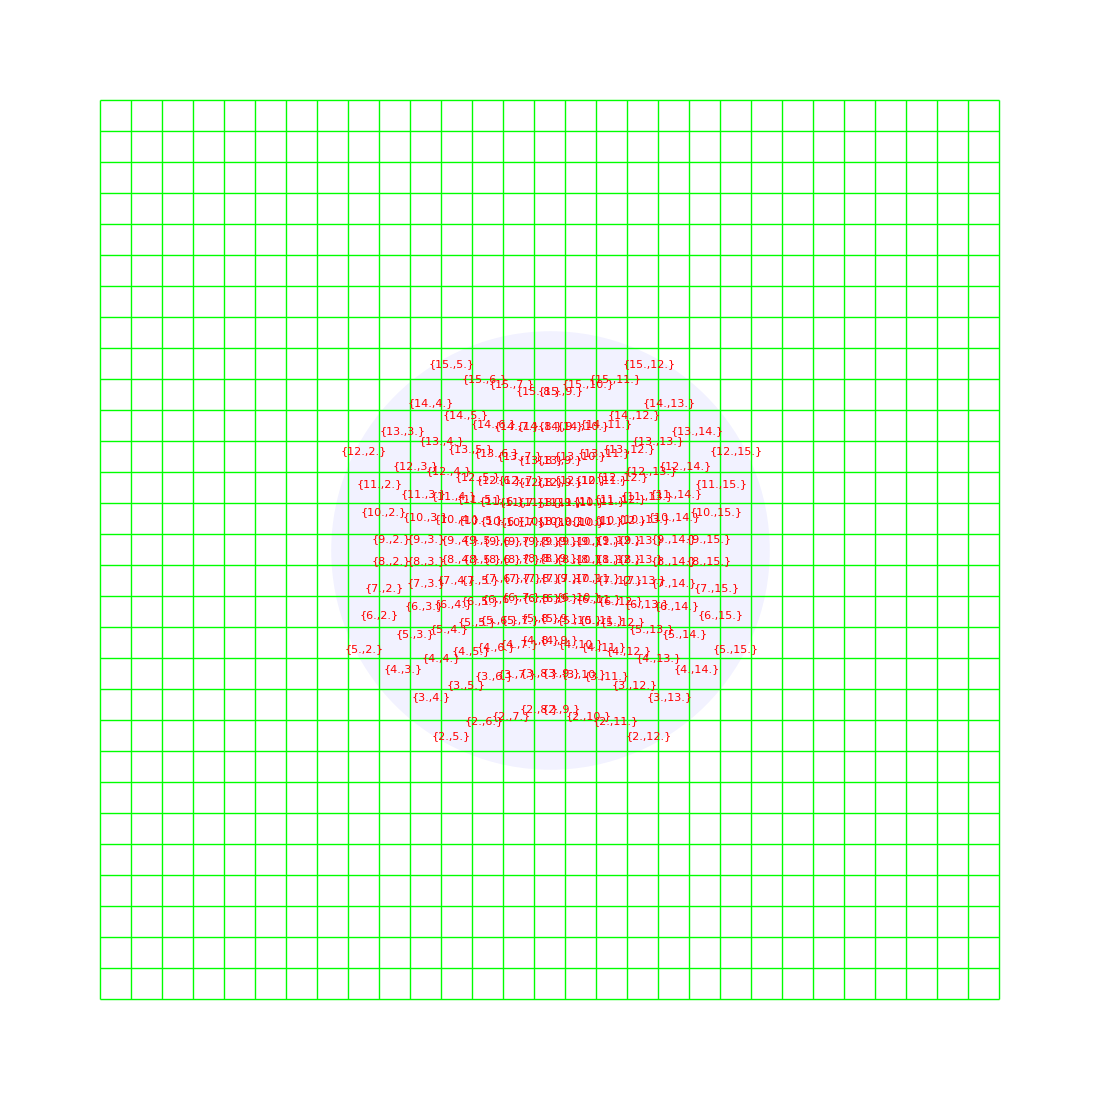

```mathematica
(*Ray positions in Entrance Face, Text shows the indices in camera pixel array*)
Print["voxPitchGraphics = ",voxPitchGraphics];
Graphics[{Blue,Opacity[0.05],Disk[Drop[volCtrGraphics,1],volCtrGraphics[[1]]Tan[ArcSin[naObj/nMedium]]],
			Green,Opacity[1],entranceFace2DGraphics,
			Red,Table[Text[camRayEntranceGraphics[[i,1]],Drop[camRayEntranceGraphics[[i,2]],1]],{i,Length[camRayEntranceGraphics]}]},
	PlotRange->All,ImageSize->1100]
```

The rays are selected to arrive at the square grid of the sensor array, 16 x 16 pixels behind a single microlens, one ray per pixel. The square geometry at the sensor plane turns into a pincushion distortion at the entrance plane to object space, due to the Abbe sine condition that is followed in the design of the microscope objective lens.

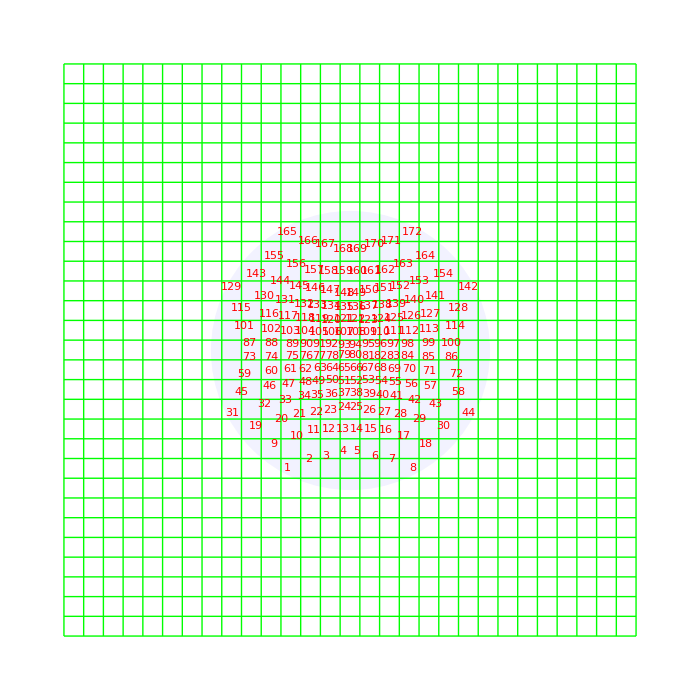

```mathematica
(*Ray positions in Entrance Face, Text shows the ray number*)
Graphics[{Blue,Opacity[0.05],Disk[Drop[volCtrGraphics,1],volCtrGraphics[[1]]Tan[ArcSin[naObj/nMedium]]],
			Green,Opacity[1],entranceFace2DGraphics,
			Red,Table[Text[i,Drop[camRayEntranceGraphics[[i,2]],1]],{i,Length[camRayEntranceGraphics]}]},
	PlotRange->All,ImageSize->700]
```

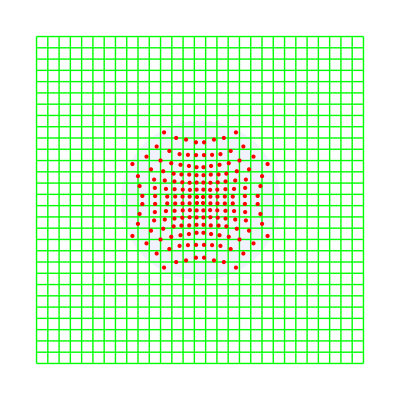

```mathematica
(*Ray positions in Entrance Face*)
Graphics[{Blue,Opacity[0.05],Disk[Drop[volCtrGraphics,1],volCtrGraphics[[1]]Tan[ArcSin[naObj/nMedium]]],
			Green,Opacity[1],entranceFace2DGraphics,
			PointSize[Large],Red,Table[Point[Drop[camRayEntranceGraphics[[i,2]],1]],{i,Length[camRayEntranceGraphics]}]},
	PlotRange->All]
```

The radius of the blue disk and range of ray positions in the entrance face scales with the refractive index (nMedium) of the object space medium and the numerical aperture (naObj) of the microscope objective. For a given naObj = 1.2 and oil (nMedium = 1.52) as the object space medium, the range is much smaller than for water (nMedium 1.33).

Radius of blue disk and range of ray positions for nMedium=1.33 and naObj=1.2

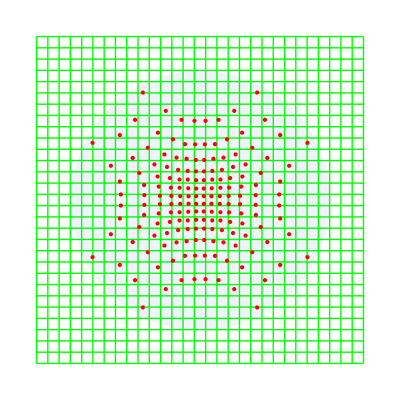

```mathematica
(*Temporarily change nMedium=1.33 and naObj=1.2 and note the difference to nMedium of oil*)
Print["Radius of blue disk and range of ray positions for nMedium=1.33 and naObj=1.2"];
tmp1=nMedium;tmp2=naObj;
nMedium=1.33;naObj=1.2;
camPixRays=Table[If[(tmp=Sqrt[(i-0.5-µLensCtr[[1]])^2+(j-0.5-µLensCtr[[2]])^2])>rNA,{Null},
	{ArcTan[i-0.5-µLensCtr[[1]],j-0.5-µLensCtr[[2]]]/Degree,ArcSin[tmp/rNA*naObj/nMedium]/Degree}//Round],{i,nrCamPix},{j,nrCamPix}];
camRayEntranceGraphics:=Flatten[Table[If[camPixRays[[i,j]]=={Null},,{{i,j},
		{0,volCtrGraphics[[1]]*Tan[camPixRays[[i,j,2]]Degree]Sin[camPixRays[[i,j,1]]Degree]+volCtrGraphics[[2]],
		volCtrGraphics[[1]]*Tan[camPixRays[[i,j,2]]Degree]Cos[camPixRays[[i,j,1]]Degree]+volCtrGraphics[[3]]}}],{i,nrCamPix},{j,nrCamPix}]//N,1]//DeleteCases[Null]
Graphics[{Blue,Opacity[0.05],Disk[Drop[volCtrGraphics,1],volCtrGraphics[[1]]Tan[ArcSin[naObj/nMedium]]],
			Green,Opacity[1],entranceFace2DGraphics,
			PointSize[Large],Red,Table[Point[Drop[camRayEntranceGraphics[[i,2]],1]],{i,Length[camRayEntranceGraphics]}]},
	PlotRange->All]
nMedium=tmp1;naObj=tmp2;
camPixRays=Table[If[(tmp=Sqrt[(i-0.5-µLensCtr[[1]])^2+(j-0.5-µLensCtr[[2]])^2])>rNA,{Null},
	{ArcTan[i-0.5-µLensCtr[[1]],j-0.5-µLensCtr[[2]]]/Degree,ArcSin[tmp/rNA*naObj/nMedium]/Degree}//Round],{i,nrCamPix},{j,nrCamPix}];
camRayEntranceGraphics:=Flatten[Table[If[camPixRays[[i,j]]=={Null},,{{i,j},
		{0,volCtrGraphics[[1]]*Tan[camPixRays[[i,j,2]]Degree]Sin[camPixRays[[i,j,1]]Degree]+volCtrGraphics[[2]],
		volCtrGraphics[[1]]*Tan[camPixRays[[i,j,2]]Degree]Cos[camPixRays[[i,j,1]]Degree]+volCtrGraphics[[3]]}}],{i,nrCamPix},{j,nrCamPix}]//N,1]//DeleteCases[Null]
```

#### Rays in object space

The graphics below shows the complete object volume, roughly 250µm x 700µm x 700µm with a blue ray and its two polarization components in red that will be turned parallel to the Y- and Z-axis after the ray is redirected by the objective lens to run parallel to the X-axis of the laboratory frame of reference.

```mathematica
rayNr=1;(*rayNr=17 is camPixRays[[4,3]], rayNr=75 extends nearly parallel to x-axis*)
Print["voxPitchGraphics = ",voxPitchGraphics];
Graphics3D[{
	Magenta,Opacity[0.2],
	objectCubeGraphics,
	Blue,Opacity[0.02],
	EdgeForm[],Cylinder[{{0,volCtr[[2]],volCtr[[3]]},{0.1,volCtr[[2]],volCtr[[3]]}},volCtr[[1]]Tan[ArcSin[naObj/nMedium]]],
	Opacity[1],Green,
	entranceFaceGraphics,
	exitFaceGraphics,
	Opacity[1],Blue,Thick,
	Arrow[{rayEnter[[rayNr]],rayExit[[rayNr]]}] ,
	Arrowheads[Medium],Red,
	tmpRotMInv=Inverse[RotationMatrix[{rayExit[[rayNr]]-rayEnter[[rayNr]],{1,0,0}}]];
	tmp1=tmpRotMInv.{0,1,0};tmp1=50tmp1/Norm[tmp1]+volCtr;
	Arrow[{volCtr,tmp1}] ,
	tmp2=tmpRotMInv.{0,0,1};tmp2=50tmp2/Norm[tmp2]+volCtr;
	Arrow[{volCtr,tmp2}] 
},Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->400]
```

voxPitchGraphics = 25

-Graphics3D-

The Y-Z object planes thisEntranceFaceGraphics and thisExitFaceGraphics illustrate the Y-Z object planes for which the ray coordinates thisRayEnter and this RayExit are calculated in the Generator routine. The two Y-Z planes  delimit the sample volume in the x-direction and the ray tracing routine is only done through voxels between these two planes.

```mathematica
(*Graphics of voxels touched by a ray, uses voxPitch for simulation*)
rayNr=1; 
smpBoxNrGraphics={5,5,5};  (*extend of sample box along X, Y, Z direction in units of voxPitchGraphics*)
smpBoxVolNrGraphics=Transpose[{voxNrCtrGraphics-smpBoxNrGraphics/2,voxNrCtrGraphics+smpBoxNrGraphics/2}]//Round;  (*sample box in object space voxel numbers*)
thisEntranceFaceGraphics={Green,Thick, (*thisEntranceFaceGraphics illustrates the Y-Z object plane for which the ray coordinates thisRayEnter are calculated in the Generator routine*)
	Line[{{smpBoxVolNrGraphics[[1,1]],0,0},{smpBoxVolNrGraphics[[1,1]],voxNrYZGraphics,0},{smpBoxVolNrGraphics[[1,1]],voxNrYZGraphics,voxNrYZGraphics},{smpBoxVolNrGraphics[[1,1]],0,voxNrYZGraphics},{smpBoxVolNrGraphics[[1,1]],0,0}}],
	Thin,Table[Line[{{0,1,0}*i+{smpBoxVolNrGraphics[[1,1]],0,0},{0,1,0}*i+{0,0,voxNrYZGraphics}+{smpBoxVolNrGraphics[[1,1]],0,0}}],{i,0,voxNrYZGraphics}],
	Table[Line[{{0,0,1}*i+{smpBoxVolNrGraphics[[1,1]],0,0},{0,0,1}*i+{0,voxNrYZGraphics,0}+{smpBoxVolNrGraphics[[1,1]],0,0}}],{i,0,voxNrYZGraphics}]};
thisExitFaceGraphics={Green,Thick, (*thisExitFaceGraphics illustrates the Y-Z object plane for which the ray coordinates thisRayExit are calculated in the Generator routine*)
	Line[{{smpBoxVolNrGraphics[[1,2]],0,0},{smpBoxVolNrGraphics[[1,2]],voxNrYZGraphics,0},{smpBoxVolNrGraphics[[1,2]],voxNrYZGraphics,voxNrYZGraphics},{smpBoxVolNrGraphics[[1,2]],0,voxNrYZGraphics},{smpBoxVolNrGraphics[[1,2]],0,0}}],
	Thin,Table[Line[{{0,1,0}*i+{smpBoxVolNrGraphics[[1,2]],0,0},{0,1,0}*i+{0,0,voxNrYZGraphics}+{smpBoxVolNrGraphics[[1,2]],0,0}}],{i,0,voxNrYZGraphics}],
	Table[Line[{{0,0,1}*i+{smpBoxVolNrGraphics[[1,2]],0,0},{0,0,1}*i+{0,voxNrYZGraphics,0}+{smpBoxVolNrGraphics[[1,2]],0,0}}],{i,0,voxNrYZGraphics}]};
Print["voxPitchGraphics = ",voxPitchGraphics,"\n","sample box = ",smpBoxVolNrGraphics, " [numbers]"];
mP0=Ceiling[midPoints[rayEnter[[rayNr]]/voxPitchGraphics,rayExit[[rayNr]]/voxPitchGraphics,{1.,1.,1.},smpBoxVolNrGraphics]];(*list of midPoint lists for every ray within naObj centered on volCtrGraphics*)
Graphics3D[{Opacity[0.25],Cuboid[Transpose[smpBoxVolNrGraphics][[1]],Transpose[smpBoxVolNrGraphics][[2]]],
		Opacity[0.5],Table[Translate[Cube[],mP0[[i]]-{0.5,0.5,0.5}],{i,Length[mP0]}],
		Opacity[1],Blue,Thick,Line[{rayEnter[[rayNr]],rayExit[[rayNr]]}/voxPitchGraphics],
		thisEntranceFaceGraphics,
		thisExitFaceGraphics},
		PlotRange->{{0,voxNrXGraphics},{0,voxNrYZGraphics},{0,voxNrYZGraphics}},ImageSize->400]
```

voxPitchGraphics = 25
sample box = {{3,8},{12,17},{12,17}} [numbers]

-Graphics3D-

#### Light Field LC-PolScope

```mathematica
fontSizeParameter=32;spread=1;
optics=Show[{
	lfSensor[34spread,0.5,"Light Field Sensor"],
	tubeLens[20spread,0.5,"Tube Lens"],
	leftCircPolar[13spread,Gray,0.5,"Left Circ. Analyzer"],
	objectiveLens[3spread,0.5],
	slideCoverslipSample[-0.5,0.5],
	condenserLens[-3spread,0.5],
	lcCompensatorBonded[-14spread,Gray,0.5,"LC-Polarizer"],
	ifFilter[-24spread,Green,0.5,"Interference Filter"],
	collectorLens[-32spread,0.5],
	bulb2[-40spread,0.5]},
PlotRange->{{-60,15},{-10,10},{-45spread,40spread}},Boxed->False,ViewPoint->{0,-Infinity,0},ImageSize->600]
```

-Graphics3D-

```mathematica
Show[optics,ViewPoint->{1.3,-2.4,2}]
```

-Graphics3D-

```mathematica
(*When calculating optics, make spread=1*)
Show[{optics,Graphics3D[{Thick,Green,Cylinder[{{0,1,-40},{0,-1,-40}},0.5],
	Line[{{-0.5,0,-40},{-4.8,0,-33},{-5.2,0,-31},{-4.8,0,-6},{-4,0,-3},{0,0,0}}],
	Line[{{0.5,0,-40},{4.8,0,-33},{5.2,0,-31},{4.8,0,-6},{4,0,-3},{0,0,0}}],
	Line[{{0,0,0},{-4,0,3},{-5.2,0,6},{-5,0,19.3},{-4.8,0,20.8},{1.1,0,35.5}}],
	Line[{{0,0,0},{4,0,3},{5.2,0,6},{5,0,19.3},{4.8,0,20.8},{-1.1,0,35.5}}],
		EdgeForm[{Thick,Opacity[1],Red}],FaceForm[Opacity[0]],Cylinder[{{0,-0.1,33.5},{0,-0.15,33.5}},7.5]}]},
	PlotRange->{{-46,15},{-10,10},{-45,42}},ImageSize->800]
```

-Graphics3D-

```mathematica
tmp=Show[{lfSensor[1.5,0.5,"NoName"],
		Graphics3D[{Green,Opacity[1],
			Thick,Line[{2.4{0.91,0,-3},{-0.91,0,3}}],
			Line[{{0.5,0,0}+2.4{0.91,0,-3},{0.5,0,0},{-0.91,0,3}}],Line[{{-0.5,0,0}+2.4{0.91,0,-3},{-0.5,0,0},{-0.91,0,3}}],
			Thick,Line[{2.4{-0.91,0,-3},{0.91,0,3}}],
			Line[{{0.5,0,0}+2.4{-0.91,0,-3},{0.5,0,0},{0.91,0,3}}],Line[{{-0.5,0,0}+2.4{-0.91,0,-3},{-0.5,0,0},{0.91,0,3}}],
			EdgeForm[{Thick,Opacity[1],Red}],FaceForm[Opacity[0]],Cylinder[{{0,-0.1,0},{0,-0.15,0}},7.5]}]},
	PlotRange->{{-7.6,7.6},{-7.6,7.6},{-7.6,7.6}},Boxed->False,ViewPoint->{0,-Infinity,0}]
```

-Graphics3D-

```mathematica
anotThick=0.002;
Show[{tmp,
	Graphics3D[{Black,Thickness[anotThick],Arrowheads[{-10anotThick,10anotThick}],
	Line[{{-1,0,3.5},{-1,0,4.5}}],Line[{{1,0,3.5},{1,0,4.5}}],Arrow[{{-1,0,4},{1,0,4}}],
	Text[Style["100µm",18,Background->White],{0,0,5}],Text[Style["16 by 16 pixels",18,Background->White],{0,0,6.2}],
	Line[{{-8,0,0},{-10,0,0}}],Line[{{-8,0,3.0},{-10,0,3.0}}],Arrow[{{-9,0,0},{-9,0,3.0}}],Text[Style["2.5mm",18,Background->White],{-9,0,1.5}]}]},
PlotRange->All]
```

-Graphics3D-

#### Schematics and Graphs for article figures

For Figure 2

```mathematica
µLenses2D[nrµL_(*odd*)]:=Module[{Δα=0.098Pi,Δx=6},{Blue,Opacity[0.5],
		Thick,Dashed,Line[{{-6,-2},{-6,2}}],Line[{{6,-2},{6,2}}],
		Table[Annulus[{-Δx i,-9},{10-0.1,10},{Pi/2-Δα,Pi/2+Δα}],{i,-(nrµL-1)/2,(nrµL-1)/2}],
		Rectangle[{-nrµL/2 Δx,-1-0.1/2},{nrµL/2 Δx,-1+0.1/2}]}]
crystal[origin_]:=Module[{xC=3,yC=1},{EdgeForm[Thickness[0.02]],LightGray,
		Parallelogram[origin-{(xC+yC)/2,yC/2},{{xC,0},{yC,yC}}],
		Black,Thickness[0.02],Dashing[{0.04,0.02}],Line[{origin+{(yC-xC)/2,yC/2}+0.7{1,-1},origin+{(yC-xC)/2,yC/2}+0.7{-1,1}}]}]
rays[origin_,rBot_,rTop_]:={Green,Thick,
		Arrow[{origin-{rBot,rBot},origin+{rTop,rTop}}],
		Arrow[{origin-{0,rBot},origin+{0,rTop}}],
		Dashed,Arrow[{origin-{-rBot,rBot},origin+{-rTop,rTop}}]}
centerPanel={µLenses2D[3],crystal[{0,0}],rays[{0,0},12,12]};
leftPanel={µLenses2D[3],crystal[{0,-6}],rays[{0,-6},6,18]};
rightPanel={µLenses2D[3],crystal[{0,6}],rays[{0,6},18,6]};
```

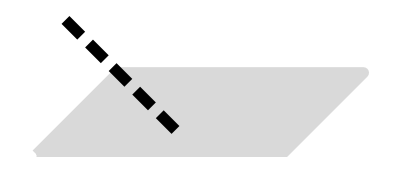

```mathematica
Graphics[crystal[0]]
```

```mathematica
Graphics[{Translate[leftPanel,{-36,0}],centerPanel,Translate[rightPanel,{36,0}],
		Style[{Text["crystal\nat z > 0",{28,6}],
			Text["nominal\nfocus plane",{-16,0}],Text["z = 0",{12,0}],
			Text["crystal\nat z < 0",{-28,-6}],
			Text["ray   1",{-7.5,6.5}],Text["2",{1,6.5}],Text["3",{5.5,6.5}]},14]
		},ImageSize->800]
```

-Graphics-

Retardance and orientation  graph for Figure 4

```mathematica
(*First lines of Simulation Cell*)
smp=shellBir[120,117,{2,0,0},35,-0.172];jjkkMinMax=Round[{0,0,26,26}];
displace={17,0 ,0 };
```

```mathematica
(ret=546Map[jMRet,ArrayFlatten[Transpose[jM4DArray],2],{2}]/(2Pi))//Raster//Graphics//ImageAdjust
```

-Graphics-

```mathematica
(azim=180Map[jMAzim,ArrayFlatten[Transpose[jM4DArray],2],{2}]/Pi+90)//Raster//Graphics//ImageAdjust
```

-Graphics-

```mathematica
retList=Table[{i,(ret[[i+2,8]]+ret[[i+2,9]])/2},{i,13}]
```

{{1,1.85078},{2,8.09596},{3,15.3277},{4,28.9397},{5,45.5246},{6,65.4907},{7,82.6709},{8,102.25},{9,154.749},{10,200.667},{11,262.857},{12,177.701},{13,108.558}}

```mathematica
azimList=Table[{i,200 (90-azim[[i+2,8]]/2-azim[[i+2,9]]/2)/90},{i,13}]
```

{{1,-1.57898×10^-14},{2,0.},{3,-1.57898×10^-14},{4,-1.57898×10^-14},{5,-1.57898×10^-14},{6,-1.57898×10^-14},{7,-1.57898×10^-14},{8,-1.57898×10^-14},{9,-1.57898×10^-14},{10,-1.57898×10^-14},{11,-1.57898×10^-14},{12,200.},{13,200.}}

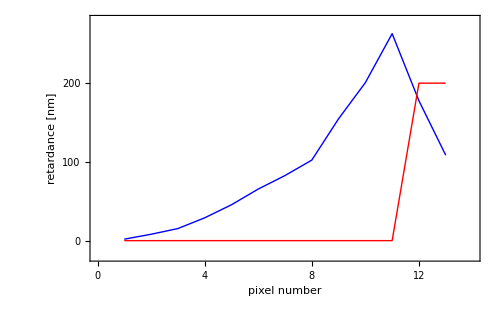

```mathematica
ListPlot[{retList,azimList},Joined->True,PlotStyle->{{Thick,Blue},{Thick,Red}},
		Frame->True,FrameStyle->Directive[Thick,32],
		FrameTicks->{{{0,100,200},{{0,"0°"},{200,"90°"}}},{{0,4,8,12},None}},
		FrameLabel->{{Style["retardance [nm]",Blue],Style["orientation",Red]},{"pixel number",None}},
		FrameTicksStyle->{{Blue,Red},{Black,None}},PlotRange->{{0,14},{-20,280}},ImageSize->500]
```

### Simulation results

#### ballBir[1,- 0.172, 10°, -90°], voxPitch = 1.73/5 = 0.347µm

```mathematica
smp=ballBir[1,-0.172,10°,-90°];
Print@@smp[[1]];
Graphics3D[Raster3D[smp[[2]]/smp[[1,8]],ColorFunction->"GrayLevelOpacity"]]
tmp2=DeleteCases[Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2],Null];
Graphics3D[{Red,Map[Line,tmp2]},ImageSize->200]
```

Ball box {X,Y,Z}={3,3,3}, radius=1.5, all in units of voxPitch=0.346667µm, birefringence=-0.172, rotation theta=10 °, rotation azim=-90 °

-Graphics3D-

-Graphics3D-

```mathematica
smp=ballBir[1,-0.172,10°,-90°];jjkkMinMax=Round[{-1,1,-1,1}];
showRetAndAzimLines[{retList,azimList},{0,0.4},2,0.9,0.004,{1,1,1},0.017,400]
```

displace = {-5 voxPitch, 0 voxPitch, 0 voxPitch}    image of retardance and azimuth lines

displace = {0 voxPitch, 0 voxPitch, 0 voxPitch}    image of retardance and azimuth lines

displace = {5 voxPitch, 0 voxPitch, 0 voxPitch}    image of retardance and azimuth lines

#### ballBir[1,- 0.172, 45°, 75°], voxPitch = 1.73/5 = 0.347µm

```mathematica
smp=ballBir[1,-0.172,45°,165°];
Print@@smp[[1]];
Graphics3D[Raster3D[smp[[2]]/smp[[1,8]],ColorFunction->"GrayLevelOpacity"]]
tmp2=DeleteCases[Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2],Null];
Graphics3D[{Red,Map[Line,tmp2]},ImageSize->200]
```

Ball box {X,Y,Z}={3,3,3}, radius=1.5, all in units of voxPitch=0.346667µm, birefringence=-0.172, rotation theta=45 °, rotation azim=165 °

-Graphics3D-

-Graphics3D-

```mathematica
?showRetAndAzimLines
```

```mathematica
smp=ballBir[1,-0.172,45°,75°];jjkkMinMax=Round[{-2,2,-2,2}];
showRetAndAzimLines[{retList,azimList},{0,0.5},2,0.9,0.004,{1,1,1},0.015,334]
```

displace = {-9, 0, 0}  retardance  image, 50nm max

displace = {-5 , 0 , 0 }  retardance  image, 50nm max

displace = {0 , 0 , 0 }   retardance  image, 50nm max

displace = {+5 , 0 , 0 }  retardance  image, 50nm max

displace = {+9 , 0 , 0 }  retardance  image, 50nm max

#### shellBir[120, 117, {2,0,0}, 35, -0.172], voxPitch = 1.73/3 = 0.5778µm

```mathematica
(*first lines of Simulation Cell*)
smp=shellBir[120,117,{2,0,0},35,-0.172];jjkkMinMax=Round[{-31,1,-1,31}];
displace={0,0 ,0 };
```

15 minutes compute time per light field array (jM4DArray)

```mathematica
(*Directory of saved JM4DArrays*)
SetDirectory["/Users/rudolfo/LightFieldMicroscopy/Article PSF of Pol-LF Experiment and Simulation/Simulations/shellBir jM4DArrays/Shell 8"];
```

displace = {-18 voxPitch, 0 voxPitch, 0 voxPitch},  jM4DArray data saved

```mathematica
jM4DArray=<<"jM4DArrayN18";
```

```mathematica
2Map[jMRet,ArrayFlatten[Transpose[jM4DArray],2],{2}]/Pi//Raster//Graphics
```

-Graphics-

```mathematica
(*2 by 4 microlenses with lines*)
jjkkMinMax=Round[{0,1,0,3}];
```

displace = {0 voxPitch, 0 voxPitch, 0 voxPitch},  jM4DArray data saved

```mathematica
jM4DArray=<<"jM4DArray0";
```

```mathematica
2Map[jMRet,ArrayFlatten[Transpose[jM4DArray],2],{2}]/Pi//Raster//Graphics
```

-Graphics-

```mathematica
(*2 by 4 microlenses with lines*)
jjkkMinMax=Round[{0,1,24,27}];
```

displace = {17 voxPitch, 0 voxPitch, 0 voxPitch},  jM4DArray data saved

```mathematica
jM4DArray=<<"jM4DArrayP17";
```

```mathematica
2Map[jMRet,ArrayFlatten[Transpose[jM4DArray],2],{2}]/Pi//Raster//Graphics
```

-Graphics-

```mathematica
(*2 by 4 microlenses with lines*)
jjkkMinMax=Round[{0,1,26,29}]
```

#### Code for generating retardance image with azim line overlay

```mathematica
Map[jMRet,ArrayFlatten[Transpose[jM4DArray],2],{2}]/Pi//Raster//Graphics
```

-Graphics-

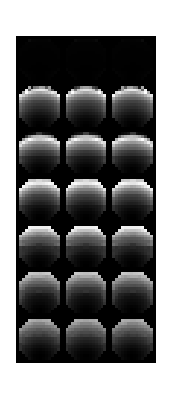

```mathematica
Map[jMRet,ArrayFlatten[Transpose[jM4DArray[[31;;33,25;;31]]],2],{2}]/Pi//Raster//Graphics
```

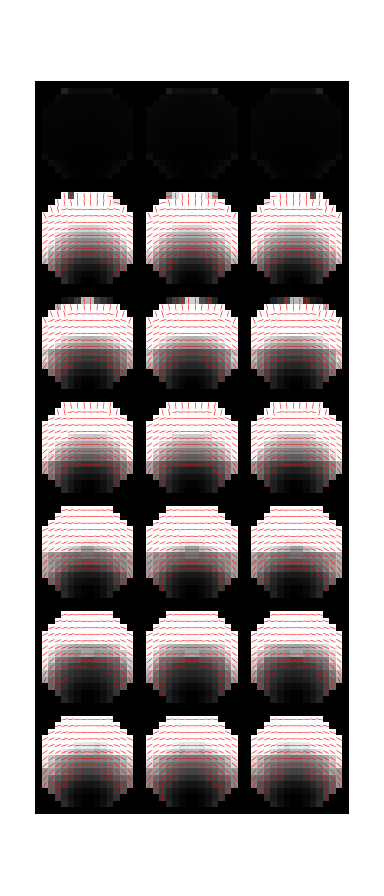

```mathematica
graphArray=jM4DArray[[31;;33,25;;31]];
(*graphArray=jM4DArray;*)
retList=Map[jMRet,ArrayFlatten[Transpose[graphArray],2],{2}];imSize=Dimensions[retList][[2]];
azimList=Map[jMAzim,ArrayFlatten[Transpose[graphArray],2],{2}];
showRetAndAzimLines[{retList,azimList},{0,1Pi},1,1,0.001,{1,1,1},0.2,8imSize]
```

```mathematica
Export["ShellSimMiddleFocus.png",%]
```

```mathematica
SetDirectory["/Users/rudolfo/Desktop"];
```

#### Code for exporting images

```mathematica
SetDirectory["/Users/rudolfo/Desktop"];
```

```mathematica
Export["SimZ+5.png",%];
```

### Playground

#### Exporting images

```mathematica
(*First, set the working directory where you will find the exported image*)
SetDirectory["/Users/rudolfo/Desktop"]
```

/Users/rudolfo/Desktop

```mathematica
voxPitch
```

0.577778

```mathematica
(*Exporting the 3D birefringence array of a sell object. All object functions generate birefringence value array as the second element at the top level*)
Export["shellBir[20,12,2,0.1]vP0.578.tiff",Image3D[shellBir[20,12,2,0.1][[2]]]//ImageAdjust]
```

shellBir[20,12,2,0.1]vP0.578.tiff

```mathematica
Export["objVolBir_vP0.578.tiff",Image3D[objVolBir[[2]]]]
```

objVolBir_vP0.578.tiff

```mathematica
Dimensions[objVolBir[[2]]]
```

{21,21,39}

```mathematica
(*Or you can paste an image directly into the Export[] function*)
Export["test.tiff",-Graphics-]
```

test.tiff

## Where do we go from here?

This ray tracing program was developed to generate polarized light field images of simulated objects of two types : 1) some objects are configured to resemble as close as possible to real objects that were observed in our experiments; 2) the program can also be used to compute polarized light light field images of arbitrary object  configurations for generating a multitude of simulated pairs of light field images and their ground truth 3D objects.

The methods in this Notebook can be extended to other anisotropies, such as linear and circular dichroism. Other assumptions and simplifications, however, such as variations of the average refractive index being small, might not be so easily extended to the more general case, such as arbitrary variations in average refractive index, as they might invalidate the assumption that rays passing through the specimen do so in straight lines. Other notes on the validity of comparing the ray tracing results to experimental polarized light field images are summarized in the Methods section of the companion article.

The ray tracing method neglects to account for the diffraction of light, including the diffraction of rays that pass through the optical system. In regular microscopy, diffraction of light on the aperture stop of the objective lens, for example, leads to effects like the Airy pattern in the image of a point source that is easily verifiable experimentally. The loss of resolution in light field imaging seems to mask these more subtle effects of the redistribution of light intensity due to diffraction. We are currently working on including diffraction into the simulation framework to further improve the similarity between experimental and simulated light field images.